Michael Barile
785
Laplacian

Parameters

none

Import Data

```mathematica
ChnlElems=Import["ChnlElems.dat"];
ChnlNodes=Import["ChnlNodes.dat"]; 

(*ChnlElems=Import["/Users/michaelbarile/Desktop/785/Laplace Project/ChnlElems.dat"];
ChnlNodes=Import["/Users/michaelbarile/Desktop/785/Laplace Project/ChnlNodes.dat"]; *)
```

Polynomial Model

```mathematica
(* basis functions *)

Subscript[n, 1][x_,y_,α_,β_,γ_,δ_]:=(γ-x)(δ-y)/((γ-α)(δ-β));
Subscript[n, 2][x_,y_,α_,β_,γ_,δ_]:=(x-α)(δ-y)/((γ-α)(δ-β));
Subscript[n, 3][x_,y_,α_,β_,γ_,δ_]:=(x-α)(y-β)/((γ-α)(δ-β));
Subscript[n, 4][x_,y_,α_,β_,γ_,δ_]:=(γ-x)(y-β)/((γ-α)(δ-β));
```

Global Matrix

```mathematica
(* initializing global matrix of all zeros *)

globalK={};
For[i=1,i≤Length[ChnlNodes],++i,
irow={};
For[j=1,j≤Length[ChnlNodes],++j,
AppendTo[irow,0]
];
AppendTo[globalK,irow]
];

(* constructing global K matrix *)

For[i=1,i≤Length[ChnlElems],++i,
Subscript[x, 1]=-0.5773502691896257;
Subscript[x, 2]=0.5773502691896257;
Subscript[y, 1]=-0.5773502691896257;
Subscript[y, 2]=0.5773502691896257;
αv=ChnlNodes[[ChnlElems[[i]][[2]]]][[2]];
βv=ChnlNodes[[ChnlElems[[i]][[2]]]][[3]];
γv=ChnlNodes[[ChnlElems[[i]][[4]]]][[2]];
δv=ChnlNodes[[ChnlElems[[i]][[4]]]][[3]];
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
For[k=1,k≤4,++k,
For[j=1,j≤4,++j,
temp[x_,y_]=D[Subscript[Localn, j][x,y],x]*D[Subscript[Localn, k][x,y],x]+D[Subscript[Localn, j][x,y],y]*D[Subscript[Localn, k][x,y],y];
globalK[[ChnlElems[[i]][[k+1]]]][[ChnlElems[[i]][[j+1]]]]=globalK[[ChnlElems[[i]][[k+1]]]][[ChnlElems[[i]][[j+1]]]]+((δv-βv)(γv-αv)/4)*∑_(i=1)^2 ∑_(j=1)^2 temp[((γv-αv)/2)Subscript[x, i]+ (γv+αv)/2,((δv-βv)/2)Subscript[y, j]+ (δv+βv)/2]];
];
];
```

```mathematica
(* printing output of global K matrix *)
MatrixForm[globalK]
```

(0.833333 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.5 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 0.666667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -1.66533×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.5 | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -1.66533×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -3.88578×10^-16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3.88578×10^-16 | 1.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.33333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.666667 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 1.33333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 1.33333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 1.33333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 2. | -0.333333 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 1.33333 | -0.333333 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 1.33333 | -0.333333 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 1.33333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.666667 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 1.33333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 1.33333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 1.33333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 2. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.33333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.33333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 2.66667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 3. | 0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.333333 | 1.66667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.5 | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.333333 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -0.75 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.75 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.75 | 3. | -5.82867×10^-16 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -5.82867×10^-16 | 1.5 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.66667 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3.33333 | -1.16667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1.16667 | 3. | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | 1.33333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.166667 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.833333 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | 0.333333 | -0.416667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.66667 | -0.583333 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.416667 | -5.82867×10^-16 | -0.333333 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.583333 | 1.5 | -0.166667
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.333333 | -0.166667 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.166667 | 0.666667)

R Vector and Boundary Conditions

```mathematica
(* initializing R vector of all zeros *)
rVec={};
For[i=1,i≤Length[ChnlNodes],++i,
AppendTo[rVec,0]
];
```

```mathematica
(* boundary conditions inflow using Gaussian Quadrature *)

For[i=1,i≤9,++i,
Subscript[x, 1]=-0.5773502691896257;
Subscript[x, 2]=0.5773502691896257;
αv=ChnlNodes[[ChnlElems[[i]][[2]]]][[2]];
βv=ChnlNodes[[ChnlElems[[i]][[2]]]][[3]];
γv=ChnlNodes[[ChnlElems[[i]][[4]]]][[2]];
δv=ChnlNodes[[ChnlElems[[i]][[4]]]][[3]];
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
For[j=1,j≤4,++j,
Subscript[sum, j]=((βv-δv)/2)∑_(k=1)^2 Subscript[Localn, j][αv,((βv-δv)/2)Subscript[x, k]+((βv+δv)/2)];
rVec[[ChnlElems[[i]][[j+1]]]]=rVec[[ChnlElems[[i]][[j+1]]]]+Subscript[sum, j];
];
];
```

```mathematica
(* boundary conditions outflow using Gaussian Quadrature *)

For[i=147,i≤155,++i,
Subscript[x, 1]=-0.5773502691896257;
Subscript[x, 2]=0.5773502691896257;
αv=ChnlNodes[[ChnlElems[[i]][[2]]]][[2]];
βv=ChnlNodes[[ChnlElems[[i]][[2]]]][[3]];
γv=ChnlNodes[[ChnlElems[[i]][[4]]]][[2]];
δv=ChnlNodes[[ChnlElems[[i]][[4]]]][[3]];
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
For[j=1,j≤4,++j,
Subscript[sum, j]=((δv-βv)/2)∑_(k=1)^2 Subscript[Localn, j][γv,((δv-βv)/2)Subscript[x, k]+((δv+βv)/2)];
rVec[[ChnlElems[[i]][[j+1]]]]=rVec[[ChnlElems[[i]][[j+1]]]]+Subscript[sum, j];
];
];

(* printing output of global R vector *)

MatrixForm[rVec]
```

(-0.25
-0.5
-0.5
-0.5
-0.5
-0.5
-0.5
-0.5
-0.75
-0.5
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.25
0.5
0.5
0.5
0.5
0.5
0.5
0.5
0.75
0.5)

```mathematica
(* unit vector for substitution into globalK matrix to account for Dirichlet boundary condition. *)

e61={};
For[i=1,i≤Length[ChnlNodes],++i,
If[i≠61,
AppendTo[e61,0],
AppendTo[e61,1]
];
];

globalK[[61]]=e61;
```

```mathematica
(* solving for coefficients *)
coef=LinearSolve[globalK,rVec];
```

Graphics

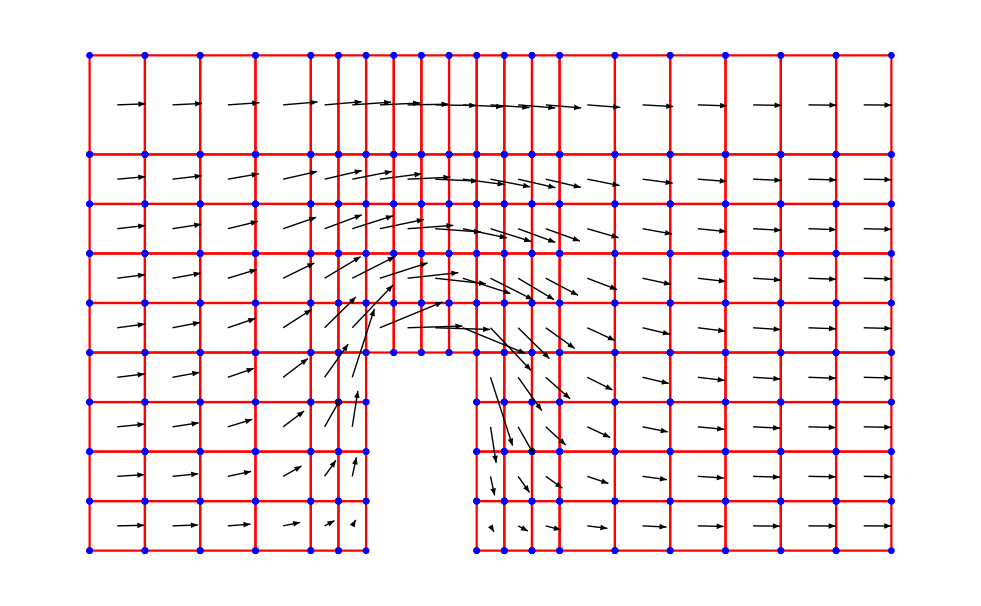

```mathematica
(* assembling grid *)

elems={};
For[i=1,i≤Length[ChnlElems],++i,
elemList={};
For[j=2,j≤5,++j,
AppendTo[elemList,{ChnlNodes[[ChnlElems[[i]][[j]]]][[2]],ChnlNodes[[ChnlElems[[i]][[j]]]][[3]]}];
];
AppendTo[elemList,elemList[[1]]
];
AppendTo[elems,elemList]
];

(* velocity vectors using bilinear interpolation *)

gradArrows={};
For[i=1,i≤Length[ChnlElems],++i,
αv=ChnlNodes[[ChnlElems[[i]][[2]]]][[2]];
βv=ChnlNodes[[ChnlElems[[i]][[2]]]][[3]];
γv=ChnlNodes[[ChnlElems[[i]][[4]]]][[2]];
δv=ChnlNodes[[ChnlElems[[i]][[4]]]][[3]];
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[i]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xCent=(αv+γv)/2;
yCent=(βv+δv)/2;
AppendTo[gradArrows,{Arrowheads[.02],Arrow[{{xCent,yCent},{xCent+g[xCent,yCent][[1]]/2,yCent+g[xCent,yCent][[2]]/2}}]}]
]; 

arrows=Graphics[gradArrows];

grid=ListPlot[elems,PlotStyle->Red,Joined->True,PlotMarkers->Graphics[{Blue,Thick,Disk[]},ImageSize->7],Axes->False];

Show[grid,arrows]
```

Streamlines

```mathematica
(* Streamline 1, element 1 *)

Δx=.001;
Δy=.001;
plots={};

αv=ChnlNodes[[ChnlElems[[1]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[1]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[1]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[1]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[1]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 1,1]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,1][[k]][[1]]≤ γv&& Subscript[pointList, 1,1][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,1],Subscript[pointList, 1,1][[k]]+g[Subscript[pointList, 1,1][[k]][[1]],Subscript[pointList, 1,1][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,1],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 10 *)

αv=ChnlNodes[[ChnlElems[[10]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[10]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[10]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[10]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[10]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,1][[Length[Subscript[pointList, 1,1]]]][[2]];
Subscript[pointList, 1,10]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,10][[k]][[1]]≤ γv&& Subscript[pointList, 1,10][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,10],Subscript[pointList, 1,10][[k]]+g[Subscript[pointList, 1,10][[k]][[1]],Subscript[pointList, 1,10][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,10],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 19 *)

αv=ChnlNodes[[ChnlElems[[19]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[19]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[19]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[19]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[19]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,10][[Length[Subscript[pointList, 1,10]]]][[2]];
Subscript[pointList, 1,19]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,19][[k]][[1]]≤ γv&& Subscript[pointList, 1,19][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,19],Subscript[pointList, 1,19][[k]]+g[Subscript[pointList, 1,19][[k]][[1]],Subscript[pointList, 1,19][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,19],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 28 *)

αv=ChnlNodes[[ChnlElems[[28]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[28]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[28]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[28]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[28]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,19][[Length[Subscript[pointList, 1,19]]]][[2]];
Subscript[pointList, 1,28]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,28][[k]][[1]]≤ γv&& Subscript[pointList, 1,28][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,28],Subscript[pointList, 1,28][[k]]+g[Subscript[pointList, 1,28][[k]][[1]],Subscript[pointList, 1,28][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,28],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 37 *)

αv=ChnlNodes[[ChnlElems[[37]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[37]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[37]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[37]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[37]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,28][[Length[Subscript[pointList, 1,28]]]][[2]];
Subscript[pointList, 1,37]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,37][[k]][[1]]≤ γv&& Subscript[pointList, 1,37][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,37],Subscript[pointList, 1,37][[k]]+g[Subscript[pointList, 1,37][[k]][[1]],Subscript[pointList, 1,37][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,37],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 38 *)

αv=ChnlNodes[[ChnlElems[[38]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[38]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[38]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[38]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[38]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 1,37][[Length[Subscript[pointList, 1,37]]]][[1]];
yStart=βv;
Subscript[pointList, 1,38]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,38][[k]][[1]]≤ γv&& Subscript[pointList, 1,38][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,38],Subscript[pointList, 1,38][[k]]+g[Subscript[pointList, 1,38][[k]][[1]],Subscript[pointList, 1,38][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,38],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 47 *)

αv=ChnlNodes[[ChnlElems[[47]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[47]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[47]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[47]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[47]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,38][[Length[Subscript[pointList, 1,38]]]][[2]];
Subscript[pointList, 1,47]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,47][[k]][[1]]≤ γv&& Subscript[pointList, 1,47][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,47],Subscript[pointList, 1,47][[k]]+g[Subscript[pointList, 1,47][[k]][[1]],Subscript[pointList, 1,47][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,47],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 48 *)

αv=ChnlNodes[[ChnlElems[[48]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[48]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[48]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[48]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[48]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 1,47][[Length[Subscript[pointList, 1,47]]]][[1]];
yStart=βv;
Subscript[pointList, 1,48]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,48][[k]][[1]]≤ γv&& Subscript[pointList, 1,48][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,48],Subscript[pointList, 1,48][[k]]+g[Subscript[pointList, 1,48][[k]][[1]],Subscript[pointList, 1,48][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,48],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 49 *)

αv=ChnlNodes[[ChnlElems[[49]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[49]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[49]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[49]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[49]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 1,48][[Length[Subscript[pointList, 1,48]]]][[1]];
yStart=βv;
Subscript[pointList, 1,49]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,49][[k]][[1]]≤ γv&& Subscript[pointList, 1,49][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,49],Subscript[pointList, 1,49][[k]]+g[Subscript[pointList, 1,49][[k]][[1]],Subscript[pointList, 1,49][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,49],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 55 *)

αv=ChnlNodes[[ChnlElems[[55]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[55]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[55]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[55]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[55]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=βv;
Subscript[pointList, 1,55]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,55][[k]][[1]]≤ γv&& Subscript[pointList, 1,55][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,55],Subscript[pointList, 1,55][[k]]+g[Subscript[pointList, 1,55][[k]][[1]],Subscript[pointList, 1,55][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,55],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 60 *)

αv=ChnlNodes[[ChnlElems[[60]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[60]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[60]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[60]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[60]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,55][[Length[Subscript[pointList, 1,55]]]][[2]];
Subscript[pointList, 1,60]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,60][[k]][[1]]≤ γv&& Subscript[pointList, 1,60][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,60],Subscript[pointList, 1,60][[k]]+g[Subscript[pointList, 1,60][[k]][[1]],Subscript[pointList, 1,60][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,60],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 65 *)

αv=ChnlNodes[[ChnlElems[[65]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[65]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[65]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[65]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[65]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,60][[Length[Subscript[pointList, 1,60]]]][[2]];
Subscript[pointList, 1,65]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,65][[k]][[1]]≤ γv&& Subscript[pointList, 1,65][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,65],Subscript[pointList, 1,65][[k]]+g[Subscript[pointList, 1,65][[k]][[1]],Subscript[pointList, 1,65][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,65],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 70 *)

αv=ChnlNodes[[ChnlElems[[70]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[70]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[70]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[70]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[70]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,65][[Length[Subscript[pointList, 1,65]]]][[2]];
Subscript[pointList, 1,70]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,70][[k]][[1]]≤ γv&& Subscript[pointList, 1,70][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 1,70],Subscript[pointList, 1,70][[k]]+g[Subscript[pointList, 1,70][[k]][[1]],Subscript[pointList, 1,70][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,70],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 78 *)

αv=ChnlNodes[[ChnlElems[[78]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[78]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[78]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[78]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[78]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=δv;
Subscript[pointList, 1,78]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,78][[k]][[1]]≤ γv&& Subscript[pointList, 1,78][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,78],Subscript[pointList, 1,78][[k]]+g[Subscript[pointList, 1,78][[k]][[1]],Subscript[pointList, 1,78][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,78],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 77 *)

αv=ChnlNodes[[ChnlElems[[77]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[77]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[77]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[77]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[77]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 1,78][[Length[Subscript[pointList, 1,78]]]][[1]];
yStart=δv;
Subscript[pointList, 1,77]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,77][[k]][[1]]≤ γv&& Subscript[pointList, 1,77][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,77],Subscript[pointList, 1,77][[k]]+g[Subscript[pointList, 1,77][[k]][[1]],Subscript[pointList, 1,77][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,77],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 76 *)

αv=ChnlNodes[[ChnlElems[[76]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[76]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[76]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[76]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[76]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 1,77][[Length[Subscript[pointList, 1,77]]]][[1]];
yStart=δv;
Subscript[pointList, 1,76]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,76][[k]][[1]]≤ γv&& Subscript[pointList, 1,76][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,76],Subscript[pointList, 1,76][[k]]+g[Subscript[pointList, 1,76][[k]][[1]],Subscript[pointList, 1,76][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,76],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 85 *)

αv=ChnlNodes[[ChnlElems[[85]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[85]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[85]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[85]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[85]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,76][[Length[Subscript[pointList, 1,76]]]][[2]];
Subscript[pointList, 1,85]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,85][[k]][[1]]≤ γv&& Subscript[pointList, 1,85][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,85],Subscript[pointList, 1,85][[k]]+g[Subscript[pointList, 1,85][[k]][[1]],Subscript[pointList, 1,85][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,85],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 84 *)

αv=ChnlNodes[[ChnlElems[[84]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[84]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[84]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[84]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[84]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 1,85][[Length[Subscript[pointList, 1,85]]]][[1]];
yStart=δv;
Subscript[pointList, 1,84]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,84][[k]][[1]]≤ γv&& Subscript[pointList, 1,84][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,84],Subscript[pointList, 1,84][[k]]+g[Subscript[pointList, 1,84][[k]][[1]],Subscript[pointList, 1,84][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,84],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 93 *)

αv=ChnlNodes[[ChnlElems[[93]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[93]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[93]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[93]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[93]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,84][[Length[Subscript[pointList, 1,84]]]][[2]];
Subscript[pointList, 1,93]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,93][[k]][[1]]≤ γv&& Subscript[pointList, 1,93][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,93],Subscript[pointList, 1,93][[k]]+g[Subscript[pointList, 1,93][[k]][[1]],Subscript[pointList, 1,93][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,93],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 102 *)

αv=ChnlNodes[[ChnlElems[[102]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[102]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[102]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[102]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[102]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,93][[Length[Subscript[pointList, 1,93]]]][[2]];
Subscript[pointList, 1,102]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,102][[k]][[1]]≤ γv&& Subscript[pointList, 1,102][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,102],Subscript[pointList, 1,102][[k]]+g[Subscript[pointList, 1,102][[k]][[1]],Subscript[pointList, 1,102][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,102],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 111 *)

αv=ChnlNodes[[ChnlElems[[111]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[111]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[111]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[111]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[111]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,102][[Length[Subscript[pointList, 1,102]]]][[2]];
Subscript[pointList, 1,111]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,111][[k]][[1]]≤ γv&& Subscript[pointList, 1,111][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,111],Subscript[pointList, 1,111][[k]]+g[Subscript[pointList, 1,111][[k]][[1]],Subscript[pointList, 1,111][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,111],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 120 *)

αv=ChnlNodes[[ChnlElems[[120]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[120]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[120]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[120]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[120]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,111][[Length[Subscript[pointList, 1,111]]]][[2]];
Subscript[pointList, 1,120]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,120][[k]][[1]]≤ γv&& Subscript[pointList, 1,120][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,120],Subscript[pointList, 1,120][[k]]+g[Subscript[pointList, 1,120][[k]][[1]],Subscript[pointList, 1,120][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,120],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 129 *)

αv=ChnlNodes[[ChnlElems[[129]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[129]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[129]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[129]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[129]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,120][[Length[Subscript[pointList, 1,120]]]][[2]];
Subscript[pointList, 1,129]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,129][[k]][[1]]≤ γv&& Subscript[pointList, 1,129][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,129],Subscript[pointList, 1,129][[k]]+g[Subscript[pointList, 1,129][[k]][[1]],Subscript[pointList, 1,129][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,129],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 138 *)

αv=ChnlNodes[[ChnlElems[[138]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[138]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[138]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[138]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[138]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,129][[Length[Subscript[pointList, 1,129]]]][[2]];
Subscript[pointList, 1,138]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,138][[k]][[1]]≤ γv&& Subscript[pointList, 1,138][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,138],Subscript[pointList, 1,138][[k]]+g[Subscript[pointList, 1,138][[k]][[1]],Subscript[pointList, 1,138][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,138],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 1, element 147 *)

αv=ChnlNodes[[ChnlElems[[147]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[147]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[147]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[147]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[147]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 1,138][[Length[Subscript[pointList, 1,138]]]][[2]];
Subscript[pointList, 1,147]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 1,147][[k]][[1]]≤ (αv+γv)/2&& Subscript[pointList, 1,147][[k]][[2]]>= βv,
AppendTo[Subscript[pointList, 1,147],Subscript[pointList, 1,147][[k]]+g[Subscript[pointList, 1,147][[k]][[1]],Subscript[pointList, 1,147][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 1,147],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 2 *)

αv=ChnlNodes[[ChnlElems[[2]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[2]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[2]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[2]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[2]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 2,2]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,2][[k]][[1]]≤ γv&& Subscript[pointList, 2,2][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,2],Subscript[pointList, 2,2][[k]]+g[Subscript[pointList, 2,2][[k]][[1]],Subscript[pointList, 2,2][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,2],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 11 *)

αv=ChnlNodes[[ChnlElems[[11]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[11]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[11]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[11]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[11]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,2][[Length[Subscript[pointList, 2,2]]]][[2]];
Subscript[pointList, 2,11]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,11][[k]][[1]]≤ γv&& Subscript[pointList, 2,11][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,11],Subscript[pointList, 2,11][[k]]+g[Subscript[pointList, 2,11][[k]][[1]],Subscript[pointList, 2,11][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,11],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 20 *)

αv=ChnlNodes[[ChnlElems[[20]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[20]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[20]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[20]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[20]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,11][[Length[Subscript[pointList, 2,11]]]][[2]];
Subscript[pointList, 2,20]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,20][[k]][[1]]≤ γv&& Subscript[pointList, 2,20][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,20],Subscript[pointList, 2,20][[k]]+g[Subscript[pointList, 2,20][[k]][[1]],Subscript[pointList, 2,20][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,20],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 29 *)

αv=ChnlNodes[[ChnlElems[[29]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[29]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[29]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[29]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[29]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,20][[Length[Subscript[pointList, 2,20]]]][[2]];
Subscript[pointList, 2,29]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,29][[k]][[1]]≤ γv&& Subscript[pointList, 2,29][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,29],Subscript[pointList, 2,29][[k]]+g[Subscript[pointList, 2,29][[k]][[1]],Subscript[pointList, 2,29][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,29],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 30 *)

αv=ChnlNodes[[ChnlElems[[30]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[30]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[30]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[30]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[30]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 2,29][[Length[Subscript[pointList, 2,29]]]][[1]];
yStart=βv;
Subscript[pointList, 2,30]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,30][[k]][[1]]≤ γv&& Subscript[pointList, 2,30][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,30],Subscript[pointList, 2,30][[k]]+g[Subscript[pointList, 2,30][[k]][[1]],Subscript[pointList, 2,30][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,30],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 39 *)

αv=ChnlNodes[[ChnlElems[[39]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[39]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[39]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[39]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[39]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,30][[Length[Subscript[pointList, 2,30]]]][[2]];
Subscript[pointList, 2,39]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,39][[k]][[1]]≤ γv&& Subscript[pointList, 2,39][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,39],Subscript[pointList, 2,39][[k]]+g[Subscript[pointList, 2,39][[k]][[1]],Subscript[pointList, 2,39][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,39],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 40 *)

αv=ChnlNodes[[ChnlElems[[40]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[40]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[40]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[40]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[40]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 2,39][[Length[Subscript[pointList, 2,39]]]][[1]];
yStart=βv;
Subscript[pointList, 2,40]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,40][[k]][[1]]≤ γv&& Subscript[pointList, 2,40][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,40],Subscript[pointList, 2,40][[k]]+g[Subscript[pointList, 2,40][[k]][[1]],Subscript[pointList, 2,40][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,40],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 49 *)

αv=ChnlNodes[[ChnlElems[[49]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[49]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[49]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[49]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[49]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,40][[Length[Subscript[pointList, 2,40]]]][[2]];
Subscript[pointList, 2,49]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,49][[k]][[1]]≤ γv&& Subscript[pointList, 2,49][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,49],Subscript[pointList, 2,49][[k]]+g[Subscript[pointList, 2,49][[k]][[1]],Subscript[pointList, 2,49][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,49],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 50 *)

αv=ChnlNodes[[ChnlElems[[50]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[50]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[50]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[50]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[50]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 2,49][[Length[Subscript[pointList, 2,49]]]][[1]];
yStart=βv;
Subscript[pointList, 2,50]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,50][[k]][[1]]≤ γv&& Subscript[pointList, 2,50][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,50],Subscript[pointList, 2,50][[k]]+g[Subscript[pointList, 2,50][[k]][[1]],Subscript[pointList, 2,50][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,50],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 55 *)

αv=ChnlNodes[[ChnlElems[[55]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[55]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[55]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[55]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[55]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,50][[Length[Subscript[pointList, 2,50]]]][[2]];
Subscript[pointList, 2,55]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,55][[k]][[1]]≤ γv&& Subscript[pointList, 2,55][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,55],Subscript[pointList, 2,55][[k]]+g[Subscript[pointList, 2,55][[k]][[1]],Subscript[pointList, 2,55][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,55],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 60 *)

αv=ChnlNodes[[ChnlElems[[60]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[60]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[60]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[60]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[60]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,55][[Length[Subscript[pointList, 2,55]]]][[2]];
Subscript[pointList, 2,60]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,60][[k]][[1]]≤ γv&& Subscript[pointList, 2,60][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,60],Subscript[pointList, 2,60][[k]]+g[Subscript[pointList, 2,60][[k]][[1]],Subscript[pointList, 2,60][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,60],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 65 *)

αv=ChnlNodes[[ChnlElems[[65]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[65]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[65]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[65]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[65]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,60][[Length[Subscript[pointList, 2,60]]]][[2]];
Subscript[pointList, 2,65]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,65][[k]][[1]]≤ γv&& Subscript[pointList, 2,65][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 2,65],Subscript[pointList, 2,65][[k]]+g[Subscript[pointList, 2,65][[k]][[1]],Subscript[pointList, 2,65][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,65],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 70 *)

αv=ChnlNodes[[ChnlElems[[70]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[70]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[70]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[70]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[70]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,65][[Length[Subscript[pointList, 2,65]]]][[2]];
Subscript[pointList, 2,70]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,70][[k]][[1]]≤ γv&& Subscript[pointList, 2,70][[k]][[2]]<=δv,
AppendTo[Subscript[pointList, 2,70],Subscript[pointList, 2,70][[k]]+g[Subscript[pointList, 2,70][[k]][[1]],Subscript[pointList, 2,70][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,70],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 79 *)

αv=ChnlNodes[[ChnlElems[[79]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[79]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[79]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[79]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[79]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 2,70][[Length[Subscript[pointList, 2,70]]]][[2]];
Subscript[pointList, 2,79]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,79][[k]][[1]]≤ γv&& Subscript[pointList, 2,79][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,79],Subscript[pointList, 2,79][[k]]+g[Subscript[pointList, 2,79][[k]][[1]],Subscript[pointList, 2,79][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,79],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 78 *)

αv=ChnlNodes[[ChnlElems[[78]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[78]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[78]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[78]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[78]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 2,79][[Length[Subscript[pointList, 2,79]]]][[1]];

yStart=δv;
Subscript[pointList, 2,78]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,78][[k]][[1]]≤ γv&& Subscript[pointList, 2,78][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,78],Subscript[pointList, 2,78][[k]]+g[Subscript[pointList, 2,78][[k]][[1]],Subscript[pointList, 2,78][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,78],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 87 *)

αv=ChnlNodes[[ChnlElems[[87]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[87]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[87]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[87]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[87]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,78][[Length[Subscript[pointList, 2,78]]]][[2]];
Subscript[pointList, 2,87]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,87][[k]][[1]]≤ γv&& Subscript[pointList, 2,87][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,87],Subscript[pointList, 2,87][[k]]+g[Subscript[pointList, 2,87][[k]][[1]],Subscript[pointList, 2,87][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,87],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 86 *)

αv=ChnlNodes[[ChnlElems[[86]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[86]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[86]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[86]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[86]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 2,87][[Length[Subscript[pointList, 2,87]]]][[1]];

yStart=δv;
Subscript[pointList, 2,86]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,86][[k]][[1]]≤ γv&& Subscript[pointList, 2,86][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,86],Subscript[pointList, 2,86][[k]]+g[Subscript[pointList, 2,86][[k]][[1]],Subscript[pointList, 2,86][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,86],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 95 *)

αv=ChnlNodes[[ChnlElems[[95]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[95]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[95]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[95]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[95]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,86][[Length[Subscript[pointList, 2,86]]]][[2]];
Subscript[pointList, 2,95]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,95][[k]][[1]]≤ γv&& Subscript[pointList, 2,95][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,95],Subscript[pointList, 2,95][[k]]+g[Subscript[pointList, 2,95][[k]][[1]],Subscript[pointList, 2,95][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,95],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 104 *)

αv=ChnlNodes[[ChnlElems[[104]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[104]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[104]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[104]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[104]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,95][[Length[Subscript[pointList, 2,95]]]][[2]];
Subscript[pointList, 2,104]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,104][[k]][[1]]≤ γv&& Subscript[pointList, 2,104][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,104],Subscript[pointList, 2,104][[k]]+g[Subscript[pointList, 2,104][[k]][[1]],Subscript[pointList, 2,104][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,104],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 103 *)

αv=ChnlNodes[[ChnlElems[[103]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[103]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[103]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[103]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[103]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 2,104][[Length[Subscript[pointList, 2,104]]]][[1]];

yStart=δv;
Subscript[pointList, 2,103]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,103][[k]][[1]]≤ γv&& Subscript[pointList, 2,103][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,103],Subscript[pointList, 2,103][[k]]+g[Subscript[pointList, 2,103][[k]][[1]],Subscript[pointList, 2,103][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,103],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 112 *)

αv=ChnlNodes[[ChnlElems[[112]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[112]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[112]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[112]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[112]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,103][[Length[Subscript[pointList, 2,103]]]][[2]];
Subscript[pointList, 2,112]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,112][[k]][[1]]≤ γv&& Subscript[pointList, 2,112][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,112],Subscript[pointList, 2,112][[k]]+g[Subscript[pointList, 2,112][[k]][[1]],Subscript[pointList, 2,112][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,112],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 121 *)

αv=ChnlNodes[[ChnlElems[[121]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[121]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[121]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[121]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[121]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,112][[Length[Subscript[pointList, 2,112]]]][[2]];
Subscript[pointList, 2,121]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,121][[k]][[1]]≤ γv&& Subscript[pointList, 2,121][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,121],Subscript[pointList, 2,121][[k]]+g[Subscript[pointList, 2,121][[k]][[1]],Subscript[pointList, 2,121][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,121],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 130 *)

αv=ChnlNodes[[ChnlElems[[130]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[130]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[130]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[130]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[130]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,121][[Length[Subscript[pointList, 2,121]]]][[2]];
Subscript[pointList, 2,130]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,130][[k]][[1]]≤ γv&& Subscript[pointList, 2,130][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,130],Subscript[pointList, 2,130][[k]]+g[Subscript[pointList, 2,130][[k]][[1]],Subscript[pointList, 2,130][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,130],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 139 *)

αv=ChnlNodes[[ChnlElems[[139]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[139]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[139]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[139]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[139]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,130][[Length[Subscript[pointList, 2,130]]]][[2]];
Subscript[pointList, 2,139]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,139][[k]][[1]]≤ γv&& Subscript[pointList, 2,139][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,139],Subscript[pointList, 2,139][[k]]+g[Subscript[pointList, 2,139][[k]][[1]],Subscript[pointList, 2,139][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,139],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 2, element 148 *)

αv=ChnlNodes[[ChnlElems[[148]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[148]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[148]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[148]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[148]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;

yStart=Subscript[pointList, 2,139][[Length[Subscript[pointList, 2,139]]]][[2]];
Subscript[pointList, 2,148]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 2,148][[k]][[1]]≤ (γv+αv)/2&& Subscript[pointList, 2,148][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 2,148],Subscript[pointList, 2,148][[k]]+g[Subscript[pointList, 2,148][[k]][[1]],Subscript[pointList, 2,148][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 2,148],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 3 *)

αv=ChnlNodes[[ChnlElems[[3]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[3]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[3]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[3]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[3]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 3,3]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,3][[k]][[1]]≤ γv&& Subscript[pointList, 3,3][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,3],Subscript[pointList, 3,3][[k]]+g[Subscript[pointList, 3,3][[k]][[1]],Subscript[pointList, 3,3][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,3],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 12 *)

αv=ChnlNodes[[ChnlElems[[12]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[12]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[12]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[12]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[12]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,3][[Length[Subscript[pointList, 3,3]]]][[2]];
Subscript[pointList, 3,12]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,12][[k]][[1]]≤ γv&& Subscript[pointList, 3,12][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,12],Subscript[pointList, 3,12][[k]]+g[Subscript[pointList, 3,12][[k]][[1]],Subscript[pointList, 3,12][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,12],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 21 *)

αv=ChnlNodes[[ChnlElems[[21]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[21]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[21]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[21]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[21]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,12][[Length[Subscript[pointList, 3,12]]]][[2]];
Subscript[pointList, 3,21]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,21][[k]][[1]]≤ γv&& Subscript[pointList, 3,21][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,21],Subscript[pointList, 3,21][[k]]+g[Subscript[pointList, 3,21][[k]][[1]],Subscript[pointList, 3,21][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,21],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 22 *)

αv=ChnlNodes[[ChnlElems[[22]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[22]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[22]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[22]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[22]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 3,21][[Length[Subscript[pointList, 3,21]]]][[1]];
yStart=βv;
Subscript[pointList, 3,22]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,22][[k]][[1]]≤ γv&& Subscript[pointList, 3,22][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,22],Subscript[pointList, 3,22][[k]]+g[Subscript[pointList, 3,22][[k]][[1]],Subscript[pointList, 3,22][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,22],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 31 *)

αv=ChnlNodes[[ChnlElems[[31]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[31]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[31]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[31]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[31]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,22][[Length[Subscript[pointList, 3,22]]]][[2]];
Subscript[pointList, 3,31]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,31][[k]][[1]]≤ γv&& Subscript[pointList, 3,31][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,31],Subscript[pointList, 3,31][[k]]+g[Subscript[pointList, 3,31][[k]][[1]],Subscript[pointList, 3,31][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,31],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 40 *)

αv=ChnlNodes[[ChnlElems[[40]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[40]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[40]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[40]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[40]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,31][[Length[Subscript[pointList, 3,31]]]][[2]];
Subscript[pointList, 3,40]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,40][[k]][[1]]≤ γv&& Subscript[pointList, 3,40][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,40],Subscript[pointList, 3,40][[k]]+g[Subscript[pointList, 3,40][[k]][[1]],Subscript[pointList, 3,40][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,40],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 41 *)

αv=ChnlNodes[[ChnlElems[[41]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[41]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[41]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[41]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[41]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 3,40][[Length[Subscript[pointList, 3,40]]]][[1]];
yStart=βv;
Subscript[pointList, 3,41]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,41][[k]][[1]]≤ γv&& Subscript[pointList, 3,41][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,41],Subscript[pointList, 3,41][[k]]+g[Subscript[pointList, 3,41][[k]][[1]],Subscript[pointList, 3,41][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,41],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 50 *)

αv=ChnlNodes[[ChnlElems[[50]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[50]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[50]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[50]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[50]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,41][[Length[Subscript[pointList, 3,41]]]][[2]];
Subscript[pointList, 3,50]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,50][[k]][[1]]≤ γv&& Subscript[pointList, 3,50][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,50],Subscript[pointList, 3,50][[k]]+g[Subscript[pointList, 3,50][[k]][[1]],Subscript[pointList, 3,50][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,50],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 51 *)

αv=ChnlNodes[[ChnlElems[[51]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[51]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[51]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[51]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[51]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 3,50][[Length[Subscript[pointList, 3,50]]]][[1]];
yStart=βv;
Subscript[pointList, 3,51]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,51][[k]][[1]]≤ γv&& Subscript[pointList, 3,51][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,51],Subscript[pointList, 3,51][[k]]+g[Subscript[pointList, 3,51][[k]][[1]],Subscript[pointList, 3,51][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,51],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 56 *)

αv=ChnlNodes[[ChnlElems[[56]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[56]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[56]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[56]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[56]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,51][[Length[Subscript[pointList, 3,51]]]][[2]];
Subscript[pointList, 3,56]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,56][[k]][[1]]≤ γv&& Subscript[pointList, 3,56][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,56],Subscript[pointList, 3,56][[k]]+g[Subscript[pointList, 3,56][[k]][[1]],Subscript[pointList, 3,56][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,56],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 61 *)

αv=ChnlNodes[[ChnlElems[[61]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[61]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[61]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[61]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[61]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,56][[Length[Subscript[pointList, 3,56]]]][[2]];
Subscript[pointList, 3,61]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,61][[k]][[1]]≤ γv&& Subscript[pointList, 3,61][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,61],Subscript[pointList, 3,61][[k]]+g[Subscript[pointList, 3,61][[k]][[1]],Subscript[pointList, 3,61][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,61],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 66 *)

αv=ChnlNodes[[ChnlElems[[66]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[66]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[66]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[66]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[66]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,61][[Length[Subscript[pointList, 3,61]]]][[2]];
Subscript[pointList, 3,66]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,66][[k]][[1]]≤ γv&& Subscript[pointList, 3,66][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,66],Subscript[pointList, 3,66][[k]]+g[Subscript[pointList, 3,66][[k]][[1]],Subscript[pointList, 3,66][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,66],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 71 *)

αv=ChnlNodes[[ChnlElems[[71]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[71]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[71]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[71]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[71]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,66][[Length[Subscript[pointList, 3,66]]]][[2]];
Subscript[pointList, 3,71]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,71][[k]][[1]]≤ γv&& Subscript[pointList, 3,71][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 3,71],Subscript[pointList, 3,71][[k]]+g[Subscript[pointList, 3,71][[k]][[1]],Subscript[pointList, 3,71][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,71],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 80 *)

αv=ChnlNodes[[ChnlElems[[80]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[80]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[80]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[80]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[80]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,71][[Length[Subscript[pointList, 3,71]]]][[2]];
Subscript[pointList, 3,80]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,80][[k]][[1]]≤ γv&& Subscript[pointList, 3,80][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,80],Subscript[pointList, 3,80][[k]]+g[Subscript[pointList, 3,80][[k]][[1]],Subscript[pointList, 3,80][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,80],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 79 *)

αv=ChnlNodes[[ChnlElems[[79]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[79]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[79]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[79]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[79]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 3,80][[Length[Subscript[pointList, 3,80]]]][[1]];
yStart=δv;
Subscript[pointList, 3,79]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,79][[k]][[1]]≤ γv&& Subscript[pointList, 3,79][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,79],Subscript[pointList, 3,79][[k]]+g[Subscript[pointList, 3,79][[k]][[1]],Subscript[pointList, 3,79][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,79],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 88 *)

αv=ChnlNodes[[ChnlElems[[88]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[88]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[88]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[88]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[88]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,79][[Length[Subscript[pointList, 3,79]]]][[2]];
Subscript[pointList, 3,88]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,88][[k]][[1]]≤ γv&& Subscript[pointList, 3,88][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,88],Subscript[pointList, 3,88][[k]]+g[Subscript[pointList, 3,88][[k]][[1]],Subscript[pointList, 3,88][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,88],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 87 *)

αv=ChnlNodes[[ChnlElems[[87]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[87]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[87]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[87]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[87]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 3,88][[Length[Subscript[pointList, 3,88]]]][[1]];
yStart=δv;
Subscript[pointList, 3,87]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,87][[k]][[1]]≤ γv&& Subscript[pointList, 3,87][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,87],Subscript[pointList, 3,87][[k]]+g[Subscript[pointList, 3,87][[k]][[1]],Subscript[pointList, 3,87][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,87],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 96 *)

αv=ChnlNodes[[ChnlElems[[96]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[96]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[96]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[96]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[96]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,87][[Length[Subscript[pointList, 3,87]]]][[2]];
Subscript[pointList, 3,96]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,96][[k]][[1]]≤ γv&& Subscript[pointList, 3,96][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,96],Subscript[pointList, 3,96][[k]]+g[Subscript[pointList, 3,96][[k]][[1]],Subscript[pointList, 3,96][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,96],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 105 *)

αv=ChnlNodes[[ChnlElems[[105]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[105]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[105]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[105]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[105]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,96][[Length[Subscript[pointList, 3,96]]]][[2]];
Subscript[pointList, 3,105]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,105][[k]][[1]]≤ γv&& Subscript[pointList, 3,105][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,105],Subscript[pointList, 3,105][[k]]+g[Subscript[pointList, 3,105][[k]][[1]],Subscript[pointList, 3,105][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,105],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 104 *)

αv=ChnlNodes[[ChnlElems[[104]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[104]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[104]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[104]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[104]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 3,105][[Length[Subscript[pointList, 3,105]]]][[1]];
yStart=δv;
Subscript[pointList, 3,104]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,104][[k]][[1]]≤ γv&& Subscript[pointList, 3,104][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,104],Subscript[pointList, 3,104][[k]]+g[Subscript[pointList, 3,104][[k]][[1]],Subscript[pointList, 3,104][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,104],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 113 *)

αv=ChnlNodes[[ChnlElems[[113]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[113]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[113]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[113]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[113]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,104][[Length[Subscript[pointList, 3,104]]]][[2]];
Subscript[pointList, 3,113]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,113][[k]][[1]]≤ γv&& Subscript[pointList, 3,113][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,113],Subscript[pointList, 3,113][[k]]+g[Subscript[pointList, 3,113][[k]][[1]],Subscript[pointList, 3,113][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,113],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 122 *)

αv=ChnlNodes[[ChnlElems[[122]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[122]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[122]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[122]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[122]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,113][[Length[Subscript[pointList, 3,113]]]][[2]];
Subscript[pointList, 3,122]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,122][[k]][[1]]≤ γv&& Subscript[pointList, 3,122][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,122],Subscript[pointList, 3,122][[k]]+g[Subscript[pointList, 3,122][[k]][[1]],Subscript[pointList, 3,122][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,122],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 131 *)

αv=ChnlNodes[[ChnlElems[[131]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[131]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[131]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[131]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[131]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,122][[Length[Subscript[pointList, 3,122]]]][[2]];
Subscript[pointList, 3,131]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,131][[k]][[1]]≤ γv&& Subscript[pointList, 3,131][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,131],Subscript[pointList, 3,131][[k]]+g[Subscript[pointList, 3,131][[k]][[1]],Subscript[pointList, 3,131][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,131],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 140 *)

αv=ChnlNodes[[ChnlElems[[140]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[140]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[140]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[140]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[140]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,131][[Length[Subscript[pointList, 3,131]]]][[2]];
Subscript[pointList, 3,140]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,140][[k]][[1]]≤ γv&& Subscript[pointList, 3,140][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,140],Subscript[pointList, 3,140][[k]]+g[Subscript[pointList, 3,140][[k]][[1]],Subscript[pointList, 3,140][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,140],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 3, element 149 *)

αv=ChnlNodes[[ChnlElems[[149]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[149]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[149]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[149]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[149]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 3,140][[Length[Subscript[pointList, 3,140]]]][[2]];
Subscript[pointList, 3,149]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 3,149][[k]][[1]]≤ (αv+γv)/2&& Subscript[pointList, 3,149][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 3,149],Subscript[pointList, 3,149][[k]]+g[Subscript[pointList, 3,149][[k]][[1]],Subscript[pointList, 3,149][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 3,149],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 4 *)

αv=ChnlNodes[[ChnlElems[[4]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[4]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[4]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[4]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[4]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 4,4]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,4][[k]][[1]]≤ γv&& Subscript[pointList, 4,4][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,4],Subscript[pointList, 4,4][[k]]+g[Subscript[pointList, 4,4][[k]][[1]],Subscript[pointList, 4,4][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,4],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 13 *)

αv=ChnlNodes[[ChnlElems[[13]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[13]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[13]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[13]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[13]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,4][[Length[Subscript[pointList, 4,4]]]][[2]];
Subscript[pointList, 4,13]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,13][[k]][[1]]≤ γv&& Subscript[pointList, 4,13][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,13],Subscript[pointList, 4,13][[k]]+g[Subscript[pointList, 4,13][[k]][[1]],Subscript[pointList, 4,13][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,13],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 22 *)

αv=ChnlNodes[[ChnlElems[[22]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[22]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[22]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[22]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[22]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,13][[Length[Subscript[pointList, 4,13]]]][[2]];
Subscript[pointList, 4,22]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,22][[k]][[1]]≤ γv&& Subscript[pointList, 4,22][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,22],Subscript[pointList, 4,22][[k]]+g[Subscript[pointList, 4,22][[k]][[1]],Subscript[pointList, 4,22][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,22],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 23 *)

αv=ChnlNodes[[ChnlElems[[23]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[23]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[23]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[23]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[23]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 4,22][[Length[Subscript[pointList, 4,22]]]][[1]];
yStart=βv;
Subscript[pointList, 4,23]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,23][[k]][[1]]≤ γv&& Subscript[pointList, 4,23][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,23],Subscript[pointList, 4,23][[k]]+g[Subscript[pointList, 4,23][[k]][[1]],Subscript[pointList, 4,23][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,23],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 32 *)

αv=ChnlNodes[[ChnlElems[[32]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[32]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[32]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[32]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[32]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,23][[Length[Subscript[pointList, 4,23]]]][[2]];
Subscript[pointList, 4,32]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,32][[k]][[1]]≤ γv&& Subscript[pointList, 4,32][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,32],Subscript[pointList, 4,32][[k]]+g[Subscript[pointList, 4,32][[k]][[1]],Subscript[pointList, 4,32][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,32],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 41 *)

αv=ChnlNodes[[ChnlElems[[41]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[41]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[41]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[41]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[41]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,32][[Length[Subscript[pointList, 4,32]]]][[2]];
Subscript[pointList, 4,41]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,41][[k]][[1]]≤ γv&& Subscript[pointList, 4,41][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,41],Subscript[pointList, 4,41][[k]]+g[Subscript[pointList, 4,41][[k]][[1]],Subscript[pointList, 4,41][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,41],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 42 *)

αv=ChnlNodes[[ChnlElems[[42]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[42]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[42]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[42]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[42]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 4,41][[Length[Subscript[pointList, 4,41]]]][[1]];
yStart=βv;
Subscript[pointList, 4,42]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,42][[k]][[1]]≤ γv&& Subscript[pointList, 4,42][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,42],Subscript[pointList, 4,42][[k]]+g[Subscript[pointList, 4,42][[k]][[1]],Subscript[pointList, 4,42][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,42],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 51 *)

αv=ChnlNodes[[ChnlElems[[51]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[51]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[51]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[51]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[51]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,42][[Length[Subscript[pointList, 4,42]]]][[2]];
Subscript[pointList, 4,51]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,51][[k]][[1]]≤ γv&& Subscript[pointList, 4,51][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,51],Subscript[pointList, 4,51][[k]]+g[Subscript[pointList, 4,51][[k]][[1]],Subscript[pointList, 4,51][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,51],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 56 *)

αv=ChnlNodes[[ChnlElems[[56]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[56]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[56]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[56]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[56]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,51][[Length[Subscript[pointList, 4,51]]]][[2]];
Subscript[pointList, 4,56]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,56][[k]][[1]]≤ γv&& Subscript[pointList, 4,56][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,56],Subscript[pointList, 4,56][[k]]+g[Subscript[pointList, 4,56][[k]][[1]],Subscript[pointList, 4,56][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,56],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 61 *)

αv=ChnlNodes[[ChnlElems[[61]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[61]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[61]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[61]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[61]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,56][[Length[Subscript[pointList, 4,56]]]][[2]];
Subscript[pointList, 4,61]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,61][[k]][[1]]≤ γv&& Subscript[pointList, 4,61][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,61],Subscript[pointList, 4,61][[k]]+g[Subscript[pointList, 4,61][[k]][[1]],Subscript[pointList, 4,61][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,61],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 66 *)

αv=ChnlNodes[[ChnlElems[[66]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[66]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[66]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[66]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[66]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,61][[Length[Subscript[pointList, 4,61]]]][[2]];
Subscript[pointList, 4,66]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,66][[k]][[1]]≤ γv&& Subscript[pointList, 4,66][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 4,66],Subscript[pointList, 4,66][[k]]+g[Subscript[pointList, 4,66][[k]][[1]],Subscript[pointList, 4,66][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,66],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 71 *)

αv=ChnlNodes[[ChnlElems[[71]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[71]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[71]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[71]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[71]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,66][[Length[Subscript[pointList, 4,66]]]][[2]];
Subscript[pointList, 4,71]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,71][[k]][[1]]≤ γv&& Subscript[pointList, 4,71][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,71],Subscript[pointList, 4,71][[k]]+g[Subscript[pointList, 4,71][[k]][[1]],Subscript[pointList, 4,71][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,71],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 80 *)

αv=ChnlNodes[[ChnlElems[[80]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[80]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[80]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[80]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[80]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,71][[Length[Subscript[pointList, 4,71]]]][[2]];
Subscript[pointList, 4,80]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,80][[k]][[1]]≤ γv&& Subscript[pointList, 4,80][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,80],Subscript[pointList, 4,80][[k]]+g[Subscript[pointList, 4,80][[k]][[1]],Subscript[pointList, 4,80][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,80],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 89 *)

αv=ChnlNodes[[ChnlElems[[89]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[89]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[89]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[89]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[89]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,80][[Length[Subscript[pointList, 4,80]]]][[2]];
Subscript[pointList, 4,89]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,89][[k]][[1]]≤ γv&& Subscript[pointList, 4,89][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,89],Subscript[pointList, 4,89][[k]]+g[Subscript[pointList, 4,89][[k]][[1]],Subscript[pointList, 4,89][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,89],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 88 *)

αv=ChnlNodes[[ChnlElems[[88]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[88]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[88]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[88]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[88]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 4,89][[Length[Subscript[pointList, 4,89]]]][[1]];
yStart=δv;
Subscript[pointList, 4,88]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,88][[k]][[1]]≤ γv&& Subscript[pointList, 4,88][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,88],Subscript[pointList, 4,88][[k]]+g[Subscript[pointList, 4,88][[k]][[1]],Subscript[pointList, 4,88][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,88],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 97 *)

αv=ChnlNodes[[ChnlElems[[97]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[97]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[97]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[97]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[97]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,88][[Length[Subscript[pointList, 4,88]]]][[2]];
Subscript[pointList, 4,97]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,97][[k]][[1]]≤ γv&& Subscript[pointList, 4,97][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,97],Subscript[pointList, 4,97][[k]]+g[Subscript[pointList, 4,97][[k]][[1]],Subscript[pointList, 4,97][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,97],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 106 *)

αv=ChnlNodes[[ChnlElems[[106]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[106]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[106]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[106]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[106]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,97][[Length[Subscript[pointList, 4,97]]]][[2]];
Subscript[pointList, 4,106]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,106][[k]][[1]]≤ γv&& Subscript[pointList, 4,106][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,106],Subscript[pointList, 4,106][[k]]+g[Subscript[pointList, 4,106][[k]][[1]],Subscript[pointList, 4,106][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,106],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 105 *)

αv=ChnlNodes[[ChnlElems[[105]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[105]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[105]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[105]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[105]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 4,106][[Length[Subscript[pointList, 4,106]]]][[1]];
yStart=δv;
Subscript[pointList, 4,105]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,105][[k]][[1]]≤ γv&& Subscript[pointList, 4,105][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,105],Subscript[pointList, 4,105][[k]]+g[Subscript[pointList, 4,105][[k]][[1]],Subscript[pointList, 4,105][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,105],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 114 *)

αv=ChnlNodes[[ChnlElems[[114]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[114]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[114]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[114]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[114]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,105][[Length[Subscript[pointList, 4,105]]]][[2]];
Subscript[pointList, 4,114]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,114][[k]][[1]]≤ γv&& Subscript[pointList, 4,114][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,114],Subscript[pointList, 4,114][[k]]+g[Subscript[pointList, 4,114][[k]][[1]],Subscript[pointList, 4,114][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,114],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 123 *)

αv=ChnlNodes[[ChnlElems[[123]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[123]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[123]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[123]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[123]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,114][[Length[Subscript[pointList, 4,114]]]][[2]];
Subscript[pointList, 4,123]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,123][[k]][[1]]≤ γv&& Subscript[pointList, 4,123][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,123],Subscript[pointList, 4,123][[k]]+g[Subscript[pointList, 4,123][[k]][[1]],Subscript[pointList, 4,123][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,123],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 132 *)

αv=ChnlNodes[[ChnlElems[[132]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[132]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[132]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[132]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[132]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,123][[Length[Subscript[pointList, 4,123]]]][[2]];
Subscript[pointList, 4,132]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,132][[k]][[1]]≤ γv&& Subscript[pointList, 4,132][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,132],Subscript[pointList, 4,132][[k]]+g[Subscript[pointList, 4,132][[k]][[1]],Subscript[pointList, 4,132][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,132],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 141 *)

αv=ChnlNodes[[ChnlElems[[141]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[141]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[141]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[141]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[141]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,132][[Length[Subscript[pointList, 4,132]]]][[2]];
Subscript[pointList, 4,141]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,141][[k]][[1]]≤ γv&& Subscript[pointList, 4,141][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,141],Subscript[pointList, 4,141][[k]]+g[Subscript[pointList, 4,141][[k]][[1]],Subscript[pointList, 4,141][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,141],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 4, element 150 *)

αv=ChnlNodes[[ChnlElems[[150]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[150]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[150]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[150]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[150]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 4,141][[Length[Subscript[pointList, 4,141]]]][[2]];
Subscript[pointList, 4,150]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 4,150][[k]][[1]]≤ (γv+αv)/2&& Subscript[pointList, 4,150][[k]][[2]]≥ βv,
AppendTo[Subscript[pointList, 4,150],Subscript[pointList, 4,150][[k]]+g[Subscript[pointList, 4,150][[k]][[1]],Subscript[pointList, 4,150][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 4,150],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 5 *)

αv=ChnlNodes[[ChnlElems[[5]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[5]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[5]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[5]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[5]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 5,5]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,5][[k]][[1]]≤ γv&& Subscript[pointList, 5,5][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,5],Subscript[pointList, 5,5][[k]]+g[Subscript[pointList, 5,5][[k]][[1]],Subscript[pointList, 5,5][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,5],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 14 *)

αv=ChnlNodes[[ChnlElems[[14]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[14]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[14]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[14]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[14]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,5][[Length[Subscript[pointList, 5,5]]]][[2]];
Subscript[pointList, 5,14]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,14][[k]][[1]]≤ γv&& Subscript[pointList, 5,14][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,14],Subscript[pointList, 5,14][[k]]+g[Subscript[pointList, 5,14][[k]][[1]],Subscript[pointList, 5,14][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,14],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 23 *)

αv=ChnlNodes[[ChnlElems[[23]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[23]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[23]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[23]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[23]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,14][[Length[Subscript[pointList, 5,14]]]][[2]];
Subscript[pointList, 5,23]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,23][[k]][[1]]≤ γv&& Subscript[pointList, 5,23][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,23],Subscript[pointList, 5,23][[k]]+g[Subscript[pointList, 5,23][[k]][[1]],Subscript[pointList, 5,23][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,23],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 24 *)

αv=ChnlNodes[[ChnlElems[[24]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[24]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[24]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[24]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[24]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 5,23][[Length[Subscript[pointList, 5,23]]]][[1]];
yStart=βv;
Subscript[pointList, 5,24]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,24][[k]][[1]]≤ γv&& Subscript[pointList, 5,24][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,24],Subscript[pointList, 5,24][[k]]+g[Subscript[pointList, 5,24][[k]][[1]],Subscript[pointList, 5,24][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,24],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 33 *)

αv=ChnlNodes[[ChnlElems[[33]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[33]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[33]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[33]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[33]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,24][[Length[Subscript[pointList, 5,24]]]][[2]];
Subscript[pointList, 5,33]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,33][[k]][[1]]≤ γv&& Subscript[pointList, 5,33][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,33],Subscript[pointList, 5,33][[k]]+g[Subscript[pointList, 5,33][[k]][[1]],Subscript[pointList, 5,33][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,33],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 42 *)

αv=ChnlNodes[[ChnlElems[[42]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[42]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[42]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[42]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[42]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,33][[Length[Subscript[pointList, 5,33]]]][[2]];
Subscript[pointList, 5,42]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,42][[k]][[1]]≤ γv&& Subscript[pointList, 5,42][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,42],Subscript[pointList, 5,42][[k]]+g[Subscript[pointList, 5,42][[k]][[1]],Subscript[pointList, 5,42][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,42],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 43 *)

αv=ChnlNodes[[ChnlElems[[43]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[43]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[43]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[43]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[43]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 5,42][[Length[Subscript[pointList, 5,42]]]][[1]];
yStart=βv;
Subscript[pointList, 5,43]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,43][[k]][[1]]≤ γv&& Subscript[pointList, 5,43][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,43],Subscript[pointList, 5,43][[k]]+g[Subscript[pointList, 5,43][[k]][[1]],Subscript[pointList, 5,43][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,43],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 52 *)

αv=ChnlNodes[[ChnlElems[[52]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[52]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[52]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[52]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[52]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,43][[Length[Subscript[pointList, 5,43]]]][[2]];
Subscript[pointList, 5,52]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,52][[k]][[1]]≤ γv&& Subscript[pointList, 5,52][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,52],Subscript[pointList, 5,52][[k]]+g[Subscript[pointList, 5,52][[k]][[1]],Subscript[pointList, 5,52][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,52],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 57 *)

αv=ChnlNodes[[ChnlElems[[57]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[57]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[57]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[57]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[57]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,52][[Length[Subscript[pointList, 5,52]]]][[2]];
Subscript[pointList, 5,57]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,57][[k]][[1]]≤ γv&& Subscript[pointList, 5,57][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,57],Subscript[pointList, 5,57][[k]]+g[Subscript[pointList, 5,57][[k]][[1]],Subscript[pointList, 5,57][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,57],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 62 *)

αv=ChnlNodes[[ChnlElems[[62]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[62]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[62]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[62]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[62]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,57][[Length[Subscript[pointList, 5,57]]]][[2]];
Subscript[pointList, 5,62]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,62][[k]][[1]]≤ γv&& Subscript[pointList, 5,62][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 5,62],Subscript[pointList, 5,62][[k]]+g[Subscript[pointList, 5,62][[k]][[1]],Subscript[pointList, 5,62][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,62],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 67 *)

αv=ChnlNodes[[ChnlElems[[67]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[67]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[67]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[67]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[67]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,62][[Length[Subscript[pointList, 5,62]]]][[2]];
Subscript[pointList, 5,67]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,67][[k]][[1]]≤ γv&& Subscript[pointList, 5,67][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,67],Subscript[pointList, 5,67][[k]]+g[Subscript[pointList, 5,67][[k]][[1]],Subscript[pointList, 5,67][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,67],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 72 *)

αv=ChnlNodes[[ChnlElems[[72]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[72]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[72]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[72]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[72]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,67][[Length[Subscript[pointList, 5,67]]]][[2]];
Subscript[pointList, 5,72]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,72][[k]][[1]]≤ γv&& Subscript[pointList, 5,72][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,72],Subscript[pointList, 5,72][[k]]+g[Subscript[pointList, 5,72][[k]][[1]],Subscript[pointList, 5,72][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,72],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 81 *)

αv=ChnlNodes[[ChnlElems[[81]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[81]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[81]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[81]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[81]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,72][[Length[Subscript[pointList, 5,72]]]][[2]];
Subscript[pointList, 5,81]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,81][[k]][[1]]≤ γv&& Subscript[pointList, 5,81][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,81],Subscript[pointList, 5,81][[k]]+g[Subscript[pointList, 5,81][[k]][[1]],Subscript[pointList, 5,81][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,81],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 90 *)

αv=ChnlNodes[[ChnlElems[[90]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[90]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[90]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[90]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[90]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,81][[Length[Subscript[pointList, 5,81]]]][[2]];
Subscript[pointList, 5,90]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,90][[k]][[1]]≤ γv&& Subscript[pointList, 5,90][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,90],Subscript[pointList, 5,90][[k]]+g[Subscript[pointList, 5,90][[k]][[1]],Subscript[pointList, 5,90][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,90],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 89 *)

αv=ChnlNodes[[ChnlElems[[89]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[89]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[89]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[89]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[89]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 5,90][[Length[Subscript[pointList, 5,90]]]][[1]];
yStart=δv;
Subscript[pointList, 5,89]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,89][[k]][[1]]≤ γv&& Subscript[pointList, 5,89][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,89],Subscript[pointList, 5,89][[k]]+g[Subscript[pointList, 5,89][[k]][[1]],Subscript[pointList, 5,89][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,89],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 98 *)

αv=ChnlNodes[[ChnlElems[[98]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[98]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[98]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[98]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[98]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,89][[Length[Subscript[pointList, 5,89]]]][[2]];
Subscript[pointList, 5,98]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,98][[k]][[1]]≤ γv&& Subscript[pointList, 5,98][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,98],Subscript[pointList, 5,98][[k]]+g[Subscript[pointList, 5,98][[k]][[1]],Subscript[pointList, 5,98][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,98],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 107 *)

αv=ChnlNodes[[ChnlElems[[107]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[107]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[107]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[107]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[107]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,98][[Length[Subscript[pointList, 5,98]]]][[2]];
Subscript[pointList, 5,107]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,107][[k]][[1]]≤ γv&& Subscript[pointList, 5,107][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,107],Subscript[pointList, 5,107][[k]]+g[Subscript[pointList, 5,107][[k]][[1]],Subscript[pointList, 5,107][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,107],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 106 *)

αv=ChnlNodes[[ChnlElems[[106]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[106]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[106]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[106]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[106]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 5,107][[Length[Subscript[pointList, 5,107]]]][[1]];
yStart=δv;
Subscript[pointList, 5,106]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,106][[k]][[1]]≤ γv&& Subscript[pointList, 5,106][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,106],Subscript[pointList, 5,106][[k]]+g[Subscript[pointList, 5,106][[k]][[1]],Subscript[pointList, 5,106][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,106],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 115 *)

αv=ChnlNodes[[ChnlElems[[115]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[115]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[115]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[115]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[115]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,106][[Length[Subscript[pointList, 5,106]]]][[2]];
Subscript[pointList, 5,115]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,115][[k]][[1]]≤ γv&& Subscript[pointList, 5,115][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,115],Subscript[pointList, 5,115][[k]]+g[Subscript[pointList, 5,115][[k]][[1]],Subscript[pointList, 5,115][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,115],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 124 *)

αv=ChnlNodes[[ChnlElems[[124]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[124]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[124]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[124]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[124]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,115][[Length[Subscript[pointList, 5,115]]]][[2]];
Subscript[pointList, 5,124]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,124][[k]][[1]]≤ γv&& Subscript[pointList, 5,124][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,124],Subscript[pointList, 5,124][[k]]+g[Subscript[pointList, 5,124][[k]][[1]],Subscript[pointList, 5,124][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,124],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 133 *)

αv=ChnlNodes[[ChnlElems[[133]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[133]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[133]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[133]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[133]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,124][[Length[Subscript[pointList, 5,124]]]][[2]];
Subscript[pointList, 5,133]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,133][[k]][[1]]≤ γv&& Subscript[pointList, 5,133][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,133],Subscript[pointList, 5,133][[k]]+g[Subscript[pointList, 5,133][[k]][[1]],Subscript[pointList, 5,133][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,133],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 142 *)

αv=ChnlNodes[[ChnlElems[[142]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[142]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[142]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[142]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[142]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,133][[Length[Subscript[pointList, 5,133]]]][[2]];
Subscript[pointList, 5,142]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,142][[k]][[1]]≤ γv&& Subscript[pointList, 5,142][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,142],Subscript[pointList, 5,142][[k]]+g[Subscript[pointList, 5,142][[k]][[1]],Subscript[pointList, 5,142][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,142],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 5, element 151 *)

αv=ChnlNodes[[ChnlElems[[151]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[151]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[151]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[151]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[151]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 5,142][[Length[Subscript[pointList, 5,142]]]][[2]];
Subscript[pointList, 5,151]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 5,151][[k]][[1]]≤ (αv+γv)/2&& Subscript[pointList, 5,151][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 5,151],Subscript[pointList, 5,151][[k]]+g[Subscript[pointList, 5,151][[k]][[1]],Subscript[pointList, 5,151][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 5,151],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 6 *)

αv=ChnlNodes[[ChnlElems[[6]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[6]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[6]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[6]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[6]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 6,6]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,6][[k]][[1]]≤ γv&& Subscript[pointList, 6,6][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,6],Subscript[pointList, 6,6][[k]]+g[Subscript[pointList, 6,6][[k]][[1]],Subscript[pointList, 6,6][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,6],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 15 *)

αv=ChnlNodes[[ChnlElems[[15]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[15]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[15]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[15]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[15]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,6][[Length[Subscript[pointList, 6,6]]]][[2]];
Subscript[pointList, 6,15]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,15][[k]][[1]]≤ γv&& Subscript[pointList, 6,15][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,15],Subscript[pointList, 6,15][[k]]+g[Subscript[pointList, 6,15][[k]][[1]],Subscript[pointList, 6,15][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,15],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 24 *)

αv=ChnlNodes[[ChnlElems[[24]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[24]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[24]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[24]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[24]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,15][[Length[Subscript[pointList, 6,15]]]][[2]];
Subscript[pointList, 6,24]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,24][[k]][[1]]≤ γv&& Subscript[pointList, 6,24][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,24],Subscript[pointList, 6,24][[k]]+g[Subscript[pointList, 6,24][[k]][[1]],Subscript[pointList, 6,24][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,24],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 25 *)

αv=ChnlNodes[[ChnlElems[[25]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[25]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[25]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[25]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[25]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 6,24][[Length[Subscript[pointList, 6,24]]]][[1]];
yStart=βv;
Subscript[pointList, 6,25]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,25][[k]][[1]]≤ γv&& Subscript[pointList, 6,25][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,25],Subscript[pointList, 6,25][[k]]+g[Subscript[pointList, 6,25][[k]][[1]],Subscript[pointList, 6,25][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,25],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 34 *)

αv=ChnlNodes[[ChnlElems[[34]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[34]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[34]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[34]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[34]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,25][[Length[Subscript[pointList, 6,25]]]][[2]];
Subscript[pointList, 6,34]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,34][[k]][[1]]≤ γv&& Subscript[pointList, 6,34][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,34],Subscript[pointList, 6,34][[k]]+g[Subscript[pointList, 6,34][[k]][[1]],Subscript[pointList, 6,34][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,34],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 43 *)

αv=ChnlNodes[[ChnlElems[[43]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[43]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[43]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[43]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[43]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,34][[Length[Subscript[pointList, 6,34]]]][[2]];
Subscript[pointList, 6,43]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,43][[k]][[1]]≤ γv&& Subscript[pointList, 6,43][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,43],Subscript[pointList, 6,43][[k]]+g[Subscript[pointList, 6,43][[k]][[1]],Subscript[pointList, 6,43][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,43],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 52 *)

αv=ChnlNodes[[ChnlElems[[52]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[52]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[52]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[52]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[52]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,43][[Length[Subscript[pointList, 6,43]]]][[2]];
Subscript[pointList, 6,52]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,52][[k]][[1]]≤ γv&& Subscript[pointList, 6,52][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,52],Subscript[pointList, 6,52][[k]]+g[Subscript[pointList, 6,52][[k]][[1]],Subscript[pointList, 6,52][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,52],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 57 *)

αv=ChnlNodes[[ChnlElems[[57]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[57]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[57]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[57]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[57]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,52][[Length[Subscript[pointList, 6,52]]]][[2]];
Subscript[pointList, 6,57]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,57][[k]][[1]]≤ γv&& Subscript[pointList, 6,57][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,57],Subscript[pointList, 6,57][[k]]+g[Subscript[pointList, 6,57][[k]][[1]],Subscript[pointList, 6,57][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,57],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 62 *)

αv=ChnlNodes[[ChnlElems[[62]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[62]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[62]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[62]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[62]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,57][[Length[Subscript[pointList, 6,57]]]][[2]];
Subscript[pointList, 6,62]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,62][[k]][[1]]≤ γv&& Subscript[pointList, 6,62][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,62],Subscript[pointList, 6,62][[k]]+g[Subscript[pointList, 6,62][[k]][[1]],Subscript[pointList, 6,62][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,62],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 63 *)

αv=ChnlNodes[[ChnlElems[[63]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[63]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[63]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[63]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[63]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 6,62][[Length[Subscript[pointList, 6,62]]]][[1]];
yStart=βv;
Subscript[pointList, 6,63]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,63][[k]][[1]]≤ γv&& Subscript[pointList, 6,63][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 6,63],Subscript[pointList, 6,63][[k]]+g[Subscript[pointList, 6,63][[k]][[1]],Subscript[pointList, 6,63][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,63],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 68 *)

αv=ChnlNodes[[ChnlElems[[68]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[68]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[68]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[68]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[68]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,63][[Length[Subscript[pointList, 6,63]]]][[2]];
Subscript[pointList, 6,68]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,68][[k]][[1]]≤ γv&& Subscript[pointList, 6,68][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,68],Subscript[pointList, 6,68][[k]]+g[Subscript[pointList, 6,68][[k]][[1]],Subscript[pointList, 6,68][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,68],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 67 *)

αv=ChnlNodes[[ChnlElems[[67]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[67]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[67]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[67]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[67]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 6,68][[Length[Subscript[pointList, 6,68]]]][[1]];
yStart=δv;
Subscript[pointList, 6,67]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,67][[k]][[1]]≤ γv&& Subscript[pointList, 6,67][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,67],Subscript[pointList, 6,67][[k]]+g[Subscript[pointList, 6,67][[k]][[1]],Subscript[pointList, 6,67][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,67],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 72 *)

αv=ChnlNodes[[ChnlElems[[72]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[72]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[72]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[72]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[72]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,67][[Length[Subscript[pointList, 6,67]]]][[2]];
Subscript[pointList, 6,72]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,72][[k]][[1]]≤ γv&& Subscript[pointList, 6,72][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,72],Subscript[pointList, 6,72][[k]]+g[Subscript[pointList, 6,72][[k]][[1]],Subscript[pointList, 6,72][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,72],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 81 *)

αv=ChnlNodes[[ChnlElems[[81]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[81]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[81]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[81]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[81]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,72][[Length[Subscript[pointList, 6,72]]]][[2]];
Subscript[pointList, 6,81]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,81][[k]][[1]]≤ γv&& Subscript[pointList, 6,81][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,81],Subscript[pointList, 6,81][[k]]+g[Subscript[pointList, 6,81][[k]][[1]],Subscript[pointList, 6,81][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,81],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 90 *)

αv=ChnlNodes[[ChnlElems[[90]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[90]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[90]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[90]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[90]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,81][[Length[Subscript[pointList, 6,81]]]][[2]];
Subscript[pointList, 6,90]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,90][[k]][[1]]≤ γv&& Subscript[pointList, 6,90][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,90],Subscript[pointList, 6,90][[k]]+g[Subscript[pointList, 6,90][[k]][[1]],Subscript[pointList, 6,90][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,90],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 99 *)

αv=ChnlNodes[[ChnlElems[[99]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[99]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[99]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[99]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[99]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,90][[Length[Subscript[pointList, 6,90]]]][[2]];
Subscript[pointList, 6,99]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,99][[k]][[1]]≤ γv&& Subscript[pointList, 6,99][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,99],Subscript[pointList, 6,99][[k]]+g[Subscript[pointList, 6,99][[k]][[1]],Subscript[pointList, 6,99][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,99],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 108 *)

αv=ChnlNodes[[ChnlElems[[108]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[108]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[108]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[108]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[108]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,99][[Length[Subscript[pointList, 6,99]]]][[2]];
Subscript[pointList, 6,108]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,108][[k]][[1]]≤ γv&& Subscript[pointList, 6,108][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,108],Subscript[pointList, 6,108][[k]]+g[Subscript[pointList, 6,108][[k]][[1]],Subscript[pointList, 6,108][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,108],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 107 *)

αv=ChnlNodes[[ChnlElems[[107]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[107]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[107]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[107]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[107]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 6,108][[Length[Subscript[pointList, 6,108]]]][[1]];
yStart=δv;
Subscript[pointList, 6,107]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,107][[k]][[1]]≤ γv&& Subscript[pointList, 6,107][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,107],Subscript[pointList, 6,107][[k]]+g[Subscript[pointList, 6,107][[k]][[1]],Subscript[pointList, 6,107][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,107],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 116 *)

αv=ChnlNodes[[ChnlElems[[116]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[116]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[116]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[116]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[116]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,107][[Length[Subscript[pointList, 6,107]]]][[2]];
Subscript[pointList, 6,116]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,116][[k]][[1]]≤ γv&& Subscript[pointList, 6,116][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,116],Subscript[pointList, 6,116][[k]]+g[Subscript[pointList, 6,116][[k]][[1]],Subscript[pointList, 6,116][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,116],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 125 *)

αv=ChnlNodes[[ChnlElems[[125]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[125]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[125]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[125]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[125]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,116][[Length[Subscript[pointList, 6,116]]]][[2]];
Subscript[pointList, 6,125]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,125][[k]][[1]]≤ γv&& Subscript[pointList, 6,125][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,125],Subscript[pointList, 6,125][[k]]+g[Subscript[pointList, 6,125][[k]][[1]],Subscript[pointList, 6,125][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,125],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 134 *)

αv=ChnlNodes[[ChnlElems[[134]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[134]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[134]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[134]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[134]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,125][[Length[Subscript[pointList, 6,125]]]][[2]];
Subscript[pointList, 6,134]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,134][[k]][[1]]≤ γv&& Subscript[pointList, 6,134][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,134],Subscript[pointList, 6,134][[k]]+g[Subscript[pointList, 6,134][[k]][[1]],Subscript[pointList, 6,134][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,134],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 143 *)

αv=ChnlNodes[[ChnlElems[[143]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[143]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[143]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[143]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[143]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,134][[Length[Subscript[pointList, 6,134]]]][[2]];
Subscript[pointList, 6,143]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,143][[k]][[1]]≤ γv&& Subscript[pointList, 6,143][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,143],Subscript[pointList, 6,143][[k]]+g[Subscript[pointList, 6,143][[k]][[1]],Subscript[pointList, 6,143][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,143],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 6, element 152 *)

αv=ChnlNodes[[ChnlElems[[152]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[152]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[152]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[152]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[152]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 6,143][[Length[Subscript[pointList, 6,143]]]][[2]];
Subscript[pointList, 6,152]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 6,152][[k]][[1]]≤ (αv+γv)/2&& Subscript[pointList, 6,152][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 6,152],Subscript[pointList, 6,152][[k]]+g[Subscript[pointList, 6,152][[k]][[1]],Subscript[pointList, 6,152][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 6,152],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 7 *)

αv=ChnlNodes[[ChnlElems[[7]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[7]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[7]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[7]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[7]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 7,7]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,7][[k]][[1]]≤ γv&& Subscript[pointList, 7,7][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,7],Subscript[pointList, 7,7][[k]]+g[Subscript[pointList, 7,7][[k]][[1]],Subscript[pointList, 7,7][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,7],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 16 *)

αv=ChnlNodes[[ChnlElems[[16]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[16]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[16]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[16]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[16]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,7][[Length[Subscript[pointList, 7,7]]]][[2]];
Subscript[pointList, 7,16]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,16][[k]][[1]]≤ γv&& Subscript[pointList, 7,16][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,16],Subscript[pointList, 7,16][[k]]+g[Subscript[pointList, 7,16][[k]][[1]],Subscript[pointList, 7,16][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,16],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 25 *)

αv=ChnlNodes[[ChnlElems[[25]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[25]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[25]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[25]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[25]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,16][[Length[Subscript[pointList, 7,16]]]][[2]];
Subscript[pointList, 7,25]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,25][[k]][[1]]≤ γv&& Subscript[pointList, 7,25][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,25],Subscript[pointList, 7,25][[k]]+g[Subscript[pointList, 7,25][[k]][[1]],Subscript[pointList, 7,25][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,25],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 26 *)

αv=ChnlNodes[[ChnlElems[[26]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[26]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[26]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[26]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[26]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 7,25][[Length[Subscript[pointList, 7,25]]]][[1]];
yStart=βv;
Subscript[pointList, 7,26]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,26][[k]][[1]]≤ γv&& Subscript[pointList, 7,26][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,26],Subscript[pointList, 7,26][[k]]+g[Subscript[pointList, 7,26][[k]][[1]],Subscript[pointList, 7,26][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,26],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 35 *)

αv=ChnlNodes[[ChnlElems[[35]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[35]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[35]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[35]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[35]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,26][[Length[Subscript[pointList, 7,26]]]][[2]];
Subscript[pointList, 7,35]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,35][[k]][[1]]≤ γv&& Subscript[pointList, 7,35][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,35],Subscript[pointList, 7,35][[k]]+g[Subscript[pointList, 7,35][[k]][[1]],Subscript[pointList, 7,35][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,35],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 44 *)

αv=ChnlNodes[[ChnlElems[[44]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[44]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[44]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[44]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[44]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,35][[Length[Subscript[pointList, 7,35]]]][[2]];
Subscript[pointList, 7,44]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,44][[k]][[1]]≤ γv&& Subscript[pointList, 7,44][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,44],Subscript[pointList, 7,44][[k]]+g[Subscript[pointList, 7,44][[k]][[1]],Subscript[pointList, 7,44][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,44],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 53 *)

αv=ChnlNodes[[ChnlElems[[53]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[53]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[53]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[53]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[53]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,44][[Length[Subscript[pointList, 7,44]]]][[2]];
Subscript[pointList, 7,53]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,53][[k]][[1]]≤ γv&& Subscript[pointList, 7,53][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,53],Subscript[pointList, 7,53][[k]]+g[Subscript[pointList, 7,53][[k]][[1]],Subscript[pointList, 7,53][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,53],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 58 *)

αv=ChnlNodes[[ChnlElems[[58]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[58]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[58]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[58]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[58]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,53][[Length[Subscript[pointList, 7,53]]]][[2]];
Subscript[pointList, 7,58]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,58][[k]][[1]]≤ γv&& Subscript[pointList, 7,58][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,58],Subscript[pointList, 7,58][[k]]+g[Subscript[pointList, 7,58][[k]][[1]],Subscript[pointList, 7,58][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,58],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 63 *)

αv=ChnlNodes[[ChnlElems[[63]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[63]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[63]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[63]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[63]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,58][[Length[Subscript[pointList, 7,58]]]][[2]];
Subscript[pointList, 7,63]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,63][[k]][[1]]≤ γv&& Subscript[pointList, 7,63][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 7,63],Subscript[pointList, 7,63][[k]]+g[Subscript[pointList, 7,63][[k]][[1]],Subscript[pointList, 7,63][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,63],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 68 *)

αv=ChnlNodes[[ChnlElems[[68]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[68]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[68]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[68]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[68]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,63][[Length[Subscript[pointList, 7,63]]]][[2]];
Subscript[pointList, 7,68]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,68][[k]][[1]]≤ γv&& Subscript[pointList, 7,68][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,68],Subscript[pointList, 7,68][[k]]+g[Subscript[pointList, 7,68][[k]][[1]],Subscript[pointList, 7,68][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,68],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 73 *)

αv=ChnlNodes[[ChnlElems[[73]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[73]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[73]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[73]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[73]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,68][[Length[Subscript[pointList, 7,68]]]][[2]];
Subscript[pointList, 7,73]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,73][[k]][[1]]≤ γv&& Subscript[pointList, 7,73][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,73],Subscript[pointList, 7,73][[k]]+g[Subscript[pointList, 7,73][[k]][[1]],Subscript[pointList, 7,73][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,73],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 82 *)

αv=ChnlNodes[[ChnlElems[[82]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[82]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[82]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[82]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[82]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,73][[Length[Subscript[pointList, 7,73]]]][[2]];
Subscript[pointList, 7,82]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,82][[k]][[1]]≤ γv&& Subscript[pointList, 7,82][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,82],Subscript[pointList, 7,82][[k]]+g[Subscript[pointList, 7,82][[k]][[1]],Subscript[pointList, 7,82][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,82],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 91 *)

αv=ChnlNodes[[ChnlElems[[91]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[91]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[91]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[91]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[91]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,82][[Length[Subscript[pointList, 7,82]]]][[2]];
Subscript[pointList, 7,91]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,91][[k]][[1]]≤ γv&& Subscript[pointList, 7,91][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,91],Subscript[pointList, 7,91][[k]]+g[Subscript[pointList, 7,91][[k]][[1]],Subscript[pointList, 7,91][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,91],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 100 *)

αv=ChnlNodes[[ChnlElems[[100]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[100]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[100]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[100]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[100]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,91][[Length[Subscript[pointList, 7,91]]]][[2]];
Subscript[pointList, 7,100]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,100][[k]][[1]]≤ γv&& Subscript[pointList, 7,100][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,100],Subscript[pointList, 7,100][[k]]+g[Subscript[pointList, 7,100][[k]][[1]],Subscript[pointList, 7,100][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,100],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 109 *)

αv=ChnlNodes[[ChnlElems[[109]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[109]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[109]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[109]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[109]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,100][[Length[Subscript[pointList, 7,100]]]][[2]];
Subscript[pointList, 7,109]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,109][[k]][[1]]≤ γv&& Subscript[pointList, 7,109][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,109],Subscript[pointList, 7,109][[k]]+g[Subscript[pointList, 7,109][[k]][[1]],Subscript[pointList, 7,109][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,109],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 108 *)

αv=ChnlNodes[[ChnlElems[[108]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[108]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[108]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[108]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[108]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 7,109][[Length[Subscript[pointList, 7,109]]]][[1]];
yStart=δv;
Subscript[pointList, 7,108]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,108][[k]][[1]]≤ γv&& Subscript[pointList, 7,108][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,108],Subscript[pointList, 7,108][[k]]+g[Subscript[pointList, 7,108][[k]][[1]],Subscript[pointList, 7,108][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,108],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 117 *)

αv=ChnlNodes[[ChnlElems[[117]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[117]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[117]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[117]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[117]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,108][[Length[Subscript[pointList, 7,108]]]][[2]];
Subscript[pointList, 7,117]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,117][[k]][[1]]≤ γv&& Subscript[pointList, 7,117][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,117],Subscript[pointList, 7,117][[k]]+g[Subscript[pointList, 7,117][[k]][[1]],Subscript[pointList, 7,117][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,117],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 126 *)

αv=ChnlNodes[[ChnlElems[[126]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[126]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[126]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[126]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[126]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,117][[Length[Subscript[pointList, 7,117]]]][[2]];
Subscript[pointList, 7,126]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,126][[k]][[1]]≤ γv&& Subscript[pointList, 7,126][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,126],Subscript[pointList, 7,126][[k]]+g[Subscript[pointList, 7,126][[k]][[1]],Subscript[pointList, 7,126][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,126],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 135 *)

αv=ChnlNodes[[ChnlElems[[135]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[135]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[135]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[135]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[135]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,126][[Length[Subscript[pointList, 7,126]]]][[2]];
Subscript[pointList, 7,135]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,135][[k]][[1]]≤ γv&& Subscript[pointList, 7,135][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,135],Subscript[pointList, 7,135][[k]]+g[Subscript[pointList, 7,135][[k]][[1]],Subscript[pointList, 7,135][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,135],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 144 *)

αv=ChnlNodes[[ChnlElems[[144]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[144]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[144]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[144]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[144]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,135][[Length[Subscript[pointList, 7,135]]]][[2]];
Subscript[pointList, 7,144]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,144][[k]][[1]]≤ γv&& Subscript[pointList, 7,144][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,144],Subscript[pointList, 7,144][[k]]+g[Subscript[pointList, 7,144][[k]][[1]],Subscript[pointList, 7,144][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,144],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 7, element 153 *)

αv=ChnlNodes[[ChnlElems[[153]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[153]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[153]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[153]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[153]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 7,144][[Length[Subscript[pointList, 7,144]]]][[2]];
Subscript[pointList, 7,153]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 7,153][[k]][[1]]≤ (γv+αv)/2&& Subscript[pointList, 7,153][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 7,153],Subscript[pointList, 7,153][[k]]+g[Subscript[pointList, 7,153][[k]][[1]],Subscript[pointList, 7,153][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 7,153],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 8 *)

αv=ChnlNodes[[ChnlElems[[8]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[8]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[8]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[8]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[8]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 8,8]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,8][[k]][[1]]≤ γv&& Subscript[pointList, 8,8][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 8,8],Subscript[pointList, 8,8][[k]]+g[Subscript[pointList, 8,8][[k]][[1]],Subscript[pointList, 8,8][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,8],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 17 *)

αv=ChnlNodes[[ChnlElems[[17]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[17]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[17]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[17]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[17]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,8][[Length[Subscript[pointList, 8,8]]]][[2]];
Subscript[pointList, 8,17]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,17][[k]][[1]]≤ γv&& Subscript[pointList, 8,17][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 8,17],Subscript[pointList, 8,17][[k]]+g[Subscript[pointList, 8,17][[k]][[1]],Subscript[pointList, 8,17][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,17],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 26 *)

αv=ChnlNodes[[ChnlElems[[26]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[26]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[26]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[26]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[26]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,17][[Length[Subscript[pointList, 8,17]]]][[2]];
Subscript[pointList, 8,26]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,26][[k]][[1]]≤ γv&& Subscript[pointList, 8,26][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 8,26],Subscript[pointList, 8,26][[k]]+g[Subscript[pointList, 8,26][[k]][[1]],Subscript[pointList, 8,26][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,26],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 35 *)

αv=ChnlNodes[[ChnlElems[[35]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[35]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[35]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[35]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[35]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,26][[Length[Subscript[pointList, 8,26]]]][[2]];
Subscript[pointList, 8,35]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,35][[k]][[1]]≤ γv&& Subscript[pointList, 8,35][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 8,35],Subscript[pointList, 8,35][[k]]+g[Subscript[pointList, 8,35][[k]][[1]],Subscript[pointList, 8,35][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,35],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 36 *)

αv=ChnlNodes[[ChnlElems[[36]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[36]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[36]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[36]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[36]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 8,35][[Length[Subscript[pointList, 8,35]]]][[1]];
yStart=βv;
Subscript[pointList, 8,36]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,36][[k]][[1]]≤ γv&& Subscript[pointList, 8,36][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 8,36],Subscript[pointList, 8,36][[k]]+g[Subscript[pointList, 8,36][[k]][[1]],Subscript[pointList, 8,36][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,36],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 45 *)

αv=ChnlNodes[[ChnlElems[[45]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[45]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[45]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[45]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[45]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,36][[Length[Subscript[pointList, 8,36]]]][[2]];
Subscript[pointList, 8,45]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,45][[k]][[1]]≤ γv&& Subscript[pointList, 8,45][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 8,45],Subscript[pointList, 8,45][[k]]+g[Subscript[pointList, 8,45][[k]][[1]],Subscript[pointList, 8,45][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,45],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 54 *)

αv=ChnlNodes[[ChnlElems[[54]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[54]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[54]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[54]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[54]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,45][[Length[Subscript[pointList, 8,45]]]][[2]];
Subscript[pointList, 8,54]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,54][[k]][[1]]≤ γv&& Subscript[pointList, 8,54][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,54],Subscript[pointList, 8,54][[k]]+g[Subscript[pointList, 8,54][[k]][[1]],Subscript[pointList, 8,54][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,54],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 59 *)

αv=ChnlNodes[[ChnlElems[[59]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[59]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[59]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[59]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[59]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,54][[Length[Subscript[pointList, 8,54]]]][[2]];
Subscript[pointList, 8,59]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,59][[k]][[1]]≤ γv&& Subscript[pointList, 8,59][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,59],Subscript[pointList, 8,59][[k]]+g[Subscript[pointList, 8,59][[k]][[1]],Subscript[pointList, 8,59][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,59],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 64 *)

αv=ChnlNodes[[ChnlElems[[64]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[64]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[64]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[64]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[64]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,59][[Length[Subscript[pointList, 8,59]]]][[2]];
Subscript[pointList, 8,64]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,64][[k]][[1]]≤ γv&& Subscript[pointList, 8,64][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,64],Subscript[pointList, 8,64][[k]]+g[Subscript[pointList, 8,64][[k]][[1]],Subscript[pointList, 8,64][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,64],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 69 *)

αv=ChnlNodes[[ChnlElems[[69]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[69]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[69]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[69]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[69]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,64][[Length[Subscript[pointList, 8,64]]]][[2]];
Subscript[pointList, 8,69]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,69][[k]][[1]]≤ γv&& Subscript[pointList, 8,69][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,69],Subscript[pointList, 8,69][[k]]+g[Subscript[pointList, 8,69][[k]][[1]],Subscript[pointList, 8,69][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,69],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 74 *)

αv=ChnlNodes[[ChnlElems[[74]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[74]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[74]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[74]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[74]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,69][[Length[Subscript[pointList, 8,69]]]][[2]];
Subscript[pointList, 8,74]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,74][[k]][[1]]≤ γv&& Subscript[pointList, 8,74][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,74],Subscript[pointList, 8,74][[k]]+g[Subscript[pointList, 8,74][[k]][[1]],Subscript[pointList, 8,74][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,74],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 83 *)

αv=ChnlNodes[[ChnlElems[[83]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[83]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[83]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[83]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[83]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,74][[Length[Subscript[pointList, 8,74]]]][[2]];
Subscript[pointList, 8,83]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,83][[k]][[1]]≤ γv&& Subscript[pointList, 8,83][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,83],Subscript[pointList, 8,83][[k]]+g[Subscript[pointList, 8,83][[k]][[1]],Subscript[pointList, 8,83][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,83],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 92 *)

αv=ChnlNodes[[ChnlElems[[92]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[92]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[92]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[92]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[92]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,83][[Length[Subscript[pointList, 8,83]]]][[2]];
Subscript[pointList, 8,92]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,92][[k]][[1]]≤ γv&& Subscript[pointList, 8,92][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,92],Subscript[pointList, 8,92][[k]]+g[Subscript[pointList, 8,92][[k]][[1]],Subscript[pointList, 8,92][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,92],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 101 *)

αv=ChnlNodes[[ChnlElems[[101]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[101]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[101]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[101]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[101]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,92][[Length[Subscript[pointList, 8,92]]]][[2]];
Subscript[pointList, 8,101]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,101][[k]][[1]]≤ γv&& Subscript[pointList, 8,101][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,101],Subscript[pointList, 8,101][[k]]+g[Subscript[pointList, 8,101][[k]][[1]],Subscript[pointList, 8,101][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,101],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 110 *)

αv=ChnlNodes[[ChnlElems[[110]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[110]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[110]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[110]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[110]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,101][[Length[Subscript[pointList, 8,101]]]][[2]];
Subscript[pointList, 8,110]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,110][[k]][[1]]≤ γv&& Subscript[pointList, 8,110][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,110],Subscript[pointList, 8,110][[k]]+g[Subscript[pointList, 8,110][[k]][[1]],Subscript[pointList, 8,110][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,110],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 109 *)

αv=ChnlNodes[[ChnlElems[[109]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[109]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[109]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[109]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[109]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=Subscript[pointList, 8,110][[Length[Subscript[pointList, 8,110]]]][[1]];
yStart=δv;
Subscript[pointList, 8,109]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,109][[k]][[1]]≤ γv&& Subscript[pointList, 8,109][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,109],Subscript[pointList, 8,109][[k]]+g[Subscript[pointList, 8,109][[k]][[1]],Subscript[pointList, 8,109][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,109],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 118 *)

αv=ChnlNodes[[ChnlElems[[118]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[118]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[118]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[118]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[118]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,109][[Length[Subscript[pointList, 8,109]]]][[2]];
Subscript[pointList, 8,118]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,118][[k]][[1]]≤ γv&& Subscript[pointList, 8,118][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,118],Subscript[pointList, 8,118][[k]]+g[Subscript[pointList, 8,118][[k]][[1]],Subscript[pointList, 8,118][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,118],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 127 *)

αv=ChnlNodes[[ChnlElems[[127]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[127]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[127]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[127]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[127]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,118][[Length[Subscript[pointList, 8,118]]]][[2]];
Subscript[pointList, 8,127]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,127][[k]][[1]]≤ γv&& Subscript[pointList, 8,127][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,127],Subscript[pointList, 8,127][[k]]+g[Subscript[pointList, 8,127][[k]][[1]],Subscript[pointList, 8,127][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,127],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 136 *)

αv=ChnlNodes[[ChnlElems[[136]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[136]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[136]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[136]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[136]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,127][[Length[Subscript[pointList, 8,127]]]][[2]];
Subscript[pointList, 8,136]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,136][[k]][[1]]≤ γv&& Subscript[pointList, 8,136][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,136],Subscript[pointList, 8,136][[k]]+g[Subscript[pointList, 8,136][[k]][[1]],Subscript[pointList, 8,136][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,136],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 145 *)

αv=ChnlNodes[[ChnlElems[[145]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[145]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[145]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[145]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[145]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,136][[Length[Subscript[pointList, 8,136]]]][[2]];
Subscript[pointList, 8,145]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,145][[k]][[1]]≤ γv&& Subscript[pointList, 8,145][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,145],Subscript[pointList, 8,145][[k]]+g[Subscript[pointList, 8,145][[k]][[1]],Subscript[pointList, 8,145][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,145],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 8, element 154 *)

αv=ChnlNodes[[ChnlElems[[154]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[154]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[154]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[154]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[154]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 8,145][[Length[Subscript[pointList, 8,145]]]][[2]];
Subscript[pointList, 8,154]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 8,154][[k]][[1]]≤ (αv+γv)/2&& Subscript[pointList, 8,154][[k]][[2]]>=βv,
AppendTo[Subscript[pointList, 8,154],Subscript[pointList, 8,154][[k]]+g[Subscript[pointList, 8,154][[k]][[1]],Subscript[pointList, 8,154][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 8,154],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 9 *)

αv=ChnlNodes[[ChnlElems[[9]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[9]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[9]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[9]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[9]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=(αv+γv)/2;
yStart=(βv+δv)/2;
Subscript[pointList, 9,9]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,9][[k]][[1]]≤ γv&& Subscript[pointList, 9,9][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,9],Subscript[pointList, 9,9][[k]]+g[Subscript[pointList, 9,9][[k]][[1]],Subscript[pointList, 9,9][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,9],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 18 *)

αv=ChnlNodes[[ChnlElems[[18]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[18]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[18]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[18]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[18]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,9][[Length[Subscript[pointList, 9,9]]]][[2]];
Subscript[pointList, 9,18]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,18][[k]][[1]]≤ γv&& Subscript[pointList, 9,18][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,18],Subscript[pointList, 9,18][[k]]+g[Subscript[pointList, 9,18][[k]][[1]],Subscript[pointList, 9,18][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,18],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 27 *)

αv=ChnlNodes[[ChnlElems[[27]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[27]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[27]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[27]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[27]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,18][[Length[Subscript[pointList, 9,18]]]][[2]];
Subscript[pointList, 9,27]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,27][[k]][[1]]≤ γv&& Subscript[pointList, 9,27][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,27],Subscript[pointList, 9,27][[k]]+g[Subscript[pointList, 9,27][[k]][[1]],Subscript[pointList, 9,27][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,27],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 36 *)

αv=ChnlNodes[[ChnlElems[[36]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[36]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[36]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[36]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[36]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,27][[Length[Subscript[pointList, 9,27]]]][[2]];
Subscript[pointList, 9,36]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,36][[k]][[1]]≤ γv&& Subscript[pointList, 9,36][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,36],Subscript[pointList, 9,36][[k]]+g[Subscript[pointList, 9,36][[k]][[1]],Subscript[pointList, 9,36][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,36],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 45 *)

αv=ChnlNodes[[ChnlElems[[45]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[45]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[45]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[45]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[45]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,36][[Length[Subscript[pointList, 9,36]]]][[2]];
Subscript[pointList, 9,45]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,45][[k]][[1]]≤ γv&& Subscript[pointList, 9,45][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,45],Subscript[pointList, 9,45][[k]]+g[Subscript[pointList, 9,45][[k]][[1]],Subscript[pointList, 9,45][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,45],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 54 *)

αv=ChnlNodes[[ChnlElems[[54]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[54]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[54]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[54]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[54]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,45][[Length[Subscript[pointList, 9,45]]]][[2]];
Subscript[pointList, 9,54]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,54][[k]][[1]]≤ γv&& Subscript[pointList, 9,54][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,54],Subscript[pointList, 9,54][[k]]+g[Subscript[pointList, 9,54][[k]][[1]],Subscript[pointList, 9,54][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,54],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 59 *)

αv=ChnlNodes[[ChnlElems[[59]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[59]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[59]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[59]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[59]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,54][[Length[Subscript[pointList, 9,54]]]][[2]];
Subscript[pointList, 9,59]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,59][[k]][[1]]≤ γv&& Subscript[pointList, 9,59][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,59],Subscript[pointList, 9,59][[k]]+g[Subscript[pointList, 9,59][[k]][[1]],Subscript[pointList, 9,59][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,59],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 64 *)

αv=ChnlNodes[[ChnlElems[[64]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[64]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[64]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[64]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[64]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,59][[Length[Subscript[pointList, 9,59]]]][[2]];
Subscript[pointList, 9,64]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,64][[k]][[1]]≤ γv&& Subscript[pointList, 9,64][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,64],Subscript[pointList, 9,64][[k]]+g[Subscript[pointList, 9,64][[k]][[1]],Subscript[pointList, 9,64][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,64],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 69 *)

αv=ChnlNodes[[ChnlElems[[69]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[69]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[69]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[69]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[69]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,64][[Length[Subscript[pointList, 9,64]]]][[2]];
Subscript[pointList, 9,69]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,69][[k]][[1]]≤ γv&& Subscript[pointList, 9,69][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,69],Subscript[pointList, 9,69][[k]]+g[Subscript[pointList, 9,69][[k]][[1]],Subscript[pointList, 9,69][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,69],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 74 *)

αv=ChnlNodes[[ChnlElems[[74]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[74]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[74]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[74]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[74]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,69][[Length[Subscript[pointList, 9,69]]]][[2]];
Subscript[pointList, 9,74]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,74][[k]][[1]]≤ γv&& Subscript[pointList, 9,74][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,74],Subscript[pointList, 9,74][[k]]+g[Subscript[pointList, 9,74][[k]][[1]],Subscript[pointList, 9,74][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,74],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 83 *)

αv=ChnlNodes[[ChnlElems[[83]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[83]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[83]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[83]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[83]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,74][[Length[Subscript[pointList, 9,74]]]][[2]];
Subscript[pointList, 9,83]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,83][[k]][[1]]≤ γv&& Subscript[pointList, 9,83][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,83],Subscript[pointList, 9,83][[k]]+g[Subscript[pointList, 9,83][[k]][[1]],Subscript[pointList, 9,83][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,83],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 92 *)

αv=ChnlNodes[[ChnlElems[[92]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[92]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[92]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[92]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[92]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,83][[Length[Subscript[pointList, 9,83]]]][[2]];
Subscript[pointList, 9,92]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,92][[k]][[1]]≤ γv&& Subscript[pointList, 9,92][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,92],Subscript[pointList, 9,92][[k]]+g[Subscript[pointList, 9,92][[k]][[1]],Subscript[pointList, 9,92][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,92],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 101 *)

αv=ChnlNodes[[ChnlElems[[101]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[101]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[101]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[101]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[101]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,92][[Length[Subscript[pointList, 9,92]]]][[2]];
Subscript[pointList, 9,101]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,101][[k]][[1]]≤ γv&& Subscript[pointList, 9,101][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,101],Subscript[pointList, 9,101][[k]]+g[Subscript[pointList, 9,101][[k]][[1]],Subscript[pointList, 9,101][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,101],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 110 *)

αv=ChnlNodes[[ChnlElems[[110]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[110]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[110]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[110]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[110]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,101][[Length[Subscript[pointList, 9,101]]]][[2]];
Subscript[pointList, 9,110]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,110][[k]][[1]]≤ γv&& Subscript[pointList, 9,110][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,110],Subscript[pointList, 9,110][[k]]+g[Subscript[pointList, 9,110][[k]][[1]],Subscript[pointList, 9,110][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,110],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 119 *)

αv=ChnlNodes[[ChnlElems[[119]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[119]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[119]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[119]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[119]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,110][[Length[Subscript[pointList, 9,110]]]][[2]];
Subscript[pointList, 9,119]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,119][[k]][[1]]≤ γv&& Subscript[pointList, 9,119][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,119],Subscript[pointList, 9,119][[k]]+g[Subscript[pointList, 9,119][[k]][[1]],Subscript[pointList, 9,119][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,119],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 128 *)

αv=ChnlNodes[[ChnlElems[[128]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[128]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[128]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[128]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[128]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,119][[Length[Subscript[pointList, 9,119]]]][[2]];
Subscript[pointList, 9,128]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,128][[k]][[1]]≤ γv&& Subscript[pointList, 9,128][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,128],Subscript[pointList, 9,128][[k]]+g[Subscript[pointList, 9,128][[k]][[1]],Subscript[pointList, 9,128][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,128],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 137 *)

αv=ChnlNodes[[ChnlElems[[137]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[137]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[137]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[137]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[137]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,128][[Length[Subscript[pointList, 9,128]]]][[2]];
Subscript[pointList, 9,137]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,137][[k]][[1]]≤ γv&& Subscript[pointList, 9,137][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,137],Subscript[pointList, 9,137][[k]]+g[Subscript[pointList, 9,137][[k]][[1]],Subscript[pointList, 9,137][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,137],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 146 *)

αv=ChnlNodes[[ChnlElems[[146]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[146]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[146]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[146]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[146]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,137][[Length[Subscript[pointList, 9,137]]]][[2]];
Subscript[pointList, 9,146]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,146][[k]][[1]]≤ γv&& Subscript[pointList, 9,146][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,146],Subscript[pointList, 9,146][[k]]+g[Subscript[pointList, 9,146][[k]][[1]],Subscript[pointList, 9,146][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,146],PlotStyle->PointSize[Tiny]]];
```

```mathematica
(* Streamline 9, element 155 *)

αv=ChnlNodes[[ChnlElems[[155]][[2]]]][[2]]; (* left  x-coord *)
γv=ChnlNodes[[ChnlElems[[155]][[4]]]][[2]];  (* right x-coord *)
βv=ChnlNodes[[ChnlElems[[155]][[2]]]][[3]];  (* lower y-coord *)
δv=ChnlNodes[[ChnlElems[[155]][[4]]]][[3]];   (* upper y-coord *)
For[l=1,l≤4,++l,
Subscript[Localn, l][x_,y_]=Subscript[n, l][x,y,αv,βv,γv,δv]
];
localPoly[x_,y_]=∑_(j=1)^4 coef[[ChnlElems[[155]][[j+1]]]]Subscript[Localn, j][x,y];
f[x_,y_]=D[localPoly[x,y],x];
h[x_,y_]=D[localPoly[x,y],y];
g[x_,y_]=(1/((γv-αv)(δv-βv)))({f[αv,βv],h[αv,βv]}(γv-x)(δv-y)+{f[γv,βv],h[γv,βv]}(x-αv)(δv-y)+{f[αv,δv],h[αv,δv]}(γv-x)(y-βv)+{f[γv,δv],h[γv,δv]}(x-αv)(y-βv));
xStart=αv;
yStart=Subscript[pointList, 9,146][[Length[Subscript[pointList, 9,146]]]][[2]];
Subscript[pointList, 9,155]={{xStart,yStart}};
k=1;
While[Subscript[pointList, 9,155][[k]][[1]]≤ (γv+αv)/2&& Subscript[pointList, 9,155][[k]][[2]]≤ δv,
AppendTo[Subscript[pointList, 9,155],Subscript[pointList, 9,155][[k]]+g[Subscript[pointList, 9,155][[k]][[1]],Subscript[pointList, 9,155][[k]][[2]]]*{Δx,Δy}];
k++;
];
AppendTo[plots,ListPlot[Subscript[pointList, 9,155],PlotStyle->PointSize[Tiny]]];
```

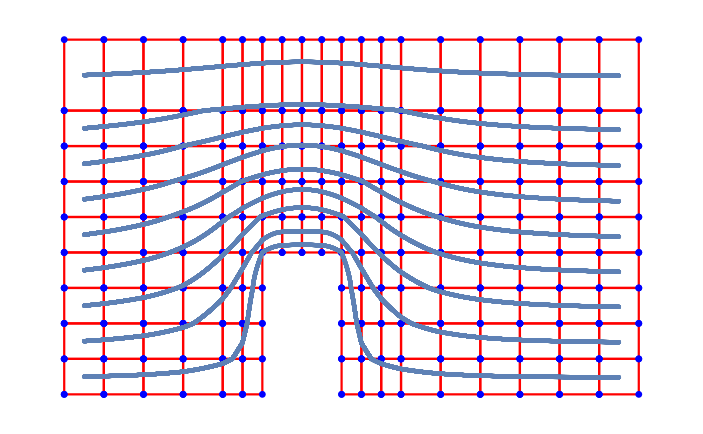

```mathematica
Show[grid,plots]
```